```mathematica
Det[{{1,0},{0,1}}-p{{G11,G12},{G12,G22}}]
```

1-G11 p-G22 p-G12^2 p^2+G11 G22 p^2

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jone_,Jtwo_,p_,z_]:=1-G11[1,Jone,Jtwo,p,z]-G22[1,Jone,Jtwo,p,z]-G12[1,Jone,Jtwo,p,z]^2+G11[1,Jone,Jtwo,p,z]G22[1,Jone,Jtwo,p,z]
```

```mathematica
Zero[J_,q_,u_] := √(J^4/(J^2+J u)+(J^3 u)/(J^2+J u)+(J^2 u^2)/(2 (J^2+J u))+(J u^3)/(8 (J^2+J u))-1/(8 (J^2+J u))(√(256 J^4 J q^2+512 J^3 J q^2 u+64 J^6 u^2+320 J^2 J q^2 u^2+96 J^5 u^3+64 J  J q^2 u^3+52 J^4 u^4+12 J^3 u^5+J^2 u^6)))
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_,Jone_,p_] := Module[{lst={{Xstart,FindRoot[Nulls[Jone,Xstart,p,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jone,Jtwoo,p,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{Jtwoo,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
ListerGreaterRange[Plusminus_,Xstart_,StartIteration_,Jone_,p_] := Module[{lst={{Xstart,FindRoot[Nulls[Jone,Xstart,p,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jone,Jtwoo,p,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{Jtwoo,a}];
,{n,1,399,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
modulerGreaterRange[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,400,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
FuegerGreaterRange[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,400,1}];
lst
]
```

```mathematica
Verlauf[HowMany_,p_] := Module[{lst={}},
For[i=0,i<HowMany,i++,
AppendTo[lst,{1,i*0.1,p}];
AppendTo[lst,Fueger[moduler[Lister[-1,-0.0005,Zero[1,i*0.1,2*p],i*0.1,p]],modulerGreaterRange[ListerGreaterRange[1,0.0005,Zero[1,i*0.1,2*p],i*0.1,p]]]]
];
l = lst
]
```

```mathematica
Verlauf[3,-0.1]
```

{{1,0.,-0.1},{{-0.0005,0.899999},{-0.001,0.899995},{-0.0015,0.899988},{-0.002,0.899978},{-0.0025,0.899966},{-0.003,0.899952},{-0.0035,0.899934},{-0.004,0.899914},{-0.0045,0.899891},{-0.005,0.899865},{-0.0055,0.899837},{-0.006,0.899806},{-0.0065,0.899773},{-0.007,0.899736},{-0.0075,0.899697},{-0.008,0.899656},{-0.0085,0.899611},{-0.009,0.899564},{-0.0095,0.899515},{-0.01,0.899462},{-0.0105,0.899407},{-0.011,0.89935},{-0.0115,0.899289},{-0.012,0.899226},{-0.0125,0.899161},{-0.013,0.899092},{-0.0135,0.899021},{-0.014,0.898948},{-0.0145,0.898872},{-0.015,0.898793},{-0.0155,0.898711},{-0.016,0.898627},{-0.0165,0.89854},{-0.017,0.898451},{-0.0175,0.898359},{-0.018,0.898264},{-0.0185,0.898167},{-0.019,0.898067},{-0.0195,0.897965},{-0.02,0.89786},{-0.0205,0.897752},{-0.021,0.897642},{-0.0215,0.897529},{-0.022,0.897414},{-0.0225,0.897296},{-0.023,0.897176},{-0.0235,0.897053},{-0.024,0.896927},{-0.0245,0.896799},{-0.025,0.896668},{-0.0255,0.896535},{-0.026,0.8964},{-0.0265,0.896261},{-0.027,0.896121},{-0.0275,0.895978},{-0.028,0.895832},{-0.0285,0.895684},{-0.029,0.895533},{-0.0295,0.89538},{-0.03,0.895225},{-0.0305,0.895067},{-0.031,0.894906},{-0.0315,0.894743},{-0.032,0.894578},{-0.0325,0.89441},{-0.033,0.89424},{-0.0335,0.894067},{-0.034,0.893892},{-0.0345,0.893715},{-0.035,0.893535},{-0.0355,0.893353},{-0.036,0.893169},{-0.0365,0.892982},{-0.037,0.892793},{-0.0375,0.892601},{-0.038,0.892407},{-0.0385,0.892211},{-0.039,0.892013},{-0.0395,0.891812},{-0.04,0.891609},{-0.0405,0.891403},{-0.041,0.891196},{-0.0415,0.890986},{-0.042,0.890773},{-0.0425,0.890559},{-0.043,0.890342},{-0.0435,0.890123},{-0.044,0.889902},{-0.0445,0.889679},{-0.045,0.889453},{-0.0455,0.889225},{-0.046,0.888995},{-0.0465,0.888763},{-0.047,0.888529},{-0.0475,0.888292},{-0.048,0.888054},{-0.0485,0.887813},{-0.049,0.88757},{-0.0495,0.887325},{-0.05,0.887078},{-0.0505,0.886829},{-0.051,0.886577},{-0.0515,0.886324},{-0.052,0.886068},{-0.0525,0.885811},{-0.053,0.885551},{-0.0535,0.885289},{-0.054,0.885025},{-0.0545,0.88476},{-0.055,0.884492},{-0.0555,0.884222},{-0.056,0.88395},{-0.0565,0.883676},{-0.057,0.883401},{-0.0575,0.883123},{-0.058,0.882843},{-0.0585,0.882562},{-0.059,0.882278},{-0.0595,0.881992},{-0.06,0.881705},{-0.0605,0.881415},{-0.061,0.881124},{-0.0615,0.880831},{-0.062,0.880536},{-0.0625,0.880239},{-0.063,0.87994},{-0.0635,0.879639},{-0.064,0.879337},{-0.0645,0.879032},{-0.065,0.878726},{-0.0655,0.878418},{-0.066,0.878108},{-0.0665,0.877796},{-0.067,0.877483},{-0.0675,0.877167},{-0.068,0.87685},{-0.0685,0.876531},{-0.069,0.876211},{-0.0695,0.875888},{-0.07,0.875564},{-0.0705,0.875238},{-0.071,0.874911},{-0.0715,0.874581},{-0.072,0.87425},{-0.0725,0.873918},{-0.073,0.873583},{-0.0735,0.873247},{-0.074,0.872909},{-0.0745,0.87257},{-0.075,0.872229},{-0.0755,0.871886},{-0.076,0.871542},{-0.0765,0.871195},{-0.077,0.870848},{-0.0775,0.870498},{-0.078,0.870148},{-0.0785,0.869795},{-0.079,0.869441},{-0.0795,0.869085},{-0.08,0.868728},{-0.0805,0.868369},{-0.081,0.868009},{-0.0815,0.867647},{-0.082,0.867283},{-0.0825,0.866918},{-0.083,0.866551},{-0.0835,0.866183},{-0.084,0.865814},{-0.0845,0.865442},{-0.085,0.86507},{-0.0855,0.864696},{-0.086,0.86432},{-0.0865,0.863943},{-0.087,0.863564},{-0.0875,0.863184},{-0.088,0.862803},{-0.0885,0.86242},{-0.089,0.862035},{-0.0895,0.861649},{-0.09,0.861262},{-0.0905,0.860873},{-0.091,0.860483},{-0.0915,0.860092},{-0.092,0.859699},{-0.0925,0.859304},{-0.093,0.858909},{-0.0935,0.858511},{-0.094,0.858113},{-0.0945,0.857713},{-0.095,0.857312},{-0.0955,0.856909},{-0.096,0.856505},{-0.0965,0.8561},{-0.097,0.855693},{-0.0975,0.855285},{-0.098,0.854876},{-0.0985,0.854466},{-0.099,0.854054},{-0.0995,0.85364},{-0.1,0.853226},{0.0005,0.899999},{0.001,0.899995},{0.0015,0.899988},{0.002,0.899978},{0.0025,0.899966},{0.003,0.899952},{0.0035,0.899934},{0.004,0.899914},{0.0045,0.899891},{0.005,0.899866},{0.0055,0.899837},{0.006,0.899807},{0.0065,0.899773},{0.007,0.899737},{0.0075,0.899698},{0.008,0.899656},{0.0085,0.899612},{0.009,0.899565},{0.0095,0.899516},{0.01,0.899464},{0.0105,0.899409},{0.011,0.899351},{0.0115,0.899291},{0.012,0.899228},{0.0125,0.899163},{0.013,0.899095},{0.0135,0.899024},{0.014,0.898951},{0.0145,0.898875},{0.015,0.898797},{0.0155,0.898716},{0.016,0.898632},{0.0165,0.898546},{0.017,0.898457},{0.0175,0.898365},{0.018,0.898271},{0.0185,0.898175},{0.019,0.898075},{0.0195,0.897974},{0.02,0.897869},{0.0205,0.897763},{0.021,0.897653},{0.0215,0.897541},{0.022,0.897427},{0.0225,0.89731},{0.023,0.89719},{0.0235,0.897068},{0.024,0.896943},{0.0245,0.896816},{0.025,0.896687},{0.0255,0.896555},{0.026,0.89642},{0.0265,0.896283},{0.027,0.896144},{0.0275,0.896002},{0.028,0.895858},{0.0285,0.895711},{0.029,0.895562},{0.0295,0.89541},{0.03,0.895256},{0.0305,0.8951},{0.031,0.894941},{0.0315,0.894779},{0.032,0.894616},{0.0325,0.89445},{0.033,0.894281},{0.0335,0.894111},{0.034,0.893938},{0.0345,0.893762},{0.035,0.893584},{0.0355,0.893404},{0.036,0.893222},{0.0365,0.893037},{0.037,0.89285},{0.0375,0.892661},{0.038,0.892469},{0.0385,0.892275},{0.039,0.892079},{0.0395,0.891881},{0.04,0.89168},{0.0405,0.891477},{0.041,0.891272},{0.0415,0.891065},{0.042,0.890856},{0.0425,0.890644},{0.043,0.89043},{0.0435,0.890214},{0.044,0.889996},{0.0445,0.889775},{0.045,0.889553},{0.0455,0.889328},{0.046,0.889101},{0.0465,0.888872},{0.047,0.888641},{0.0475,0.888408},{0.048,0.888173},{0.0485,0.887935},{0.049,0.887696},{0.0495,0.887455},{0.05,0.887211},{0.0505,0.886965},{0.051,0.886718},{0.0515,0.886468},{0.052,0.886216},{0.0525,0.885963},{0.053,0.885707},{0.0535,0.885449},{0.054,0.88519},{0.0545,0.884928},{0.055,0.884664},{0.0555,0.884399},{0.056,0.884131},{0.0565,0.883862},{0.057,0.883591},{0.0575,0.883317},{0.058,0.883042},{0.0585,0.882765},{0.059,0.882486},{0.0595,0.882205},{0.06,0.881922},{0.0605,0.881638},{0.061,0.881351},{0.0615,0.881063},{0.062,0.880773},{0.0625,0.880481},{0.063,0.880187},{0.0635,0.879892},{0.064,0.879594},{0.0645,0.879295},{0.065,0.878994},{0.0655,0.878692},{0.066,0.878387},{0.0665,0.878081},{0.067,0.877773},{0.0675,0.877463},{0.068,0.877152},{0.0685,0.876839},{0.069,0.876524},{0.0695,0.876208},{0.07,0.875889},{0.0705,0.875569},{0.071,0.875248},{0.0715,0.874925},{0.072,0.8746},{0.0725,0.874273},{0.073,0.873945},{0.0735,0.873615},{0.074,0.873284},{0.0745,0.872951},{0.075,0.872616},{0.0755,0.87228},{0.076,0.871942},{0.0765,0.871602},{0.077,0.871261},{0.0775,0.870919},{0.078,0.870575},{0.0785,0.870229},{0.079,0.869882},{0.0795,0.869533},{0.08,0.869183},{0.0805,0.868831},{0.081,0.868478},{0.0815,0.868123},{0.082,0.867766},{0.0825,0.867409},{0.083,0.867049},{0.0835,0.866689},{0.084,0.866326},{0.0845,0.865963},{0.085,0.865597},{0.0855,0.865231},{0.086,0.864863},{0.0865,0.864493},{0.087,0.864122},{0.0875,0.86375},{0.088,0.863376},{0.0885,0.863001},{0.089,0.862625},{0.0895,0.862247},{0.09,0.861868},{0.0905,0.861487},{0.091,0.861105},{0.0915,0.860721},{0.092,0.860337},{0.0925,0.859951},{0.093,0.859563},{0.0935,0.859174},{0.094,0.858784},{0.0945,0.858393},{0.095,0.858},{0.0955,0.857606},{0.096,0.857211},{0.0965,0.856814},{0.097,0.856416},{0.0975,0.856017},{0.098,0.855616},{0.0985,0.855214},{0.099,0.854811},{0.0995,0.854407},{0.1,0.854001},{0.1005,0.853595},{0.101,0.853187},{0.1015,0.852777},{0.102,0.852367},{0.1025,0.851955},{0.103,0.851542},{0.1035,0.851128},{0.104,0.850712},{0.1045,0.850296},{0.105,0.849878},{0.1055,0.849459},{0.106,0.849038},{0.1065,0.848617},{0.107,0.848194},{0.1075,0.847771},{0.108,0.847346},{0.1085,0.84692},{0.109,0.846492},{0.1095,0.846064},{0.11,0.845634},{0.1105,0.845204},{0.111,0.844772},{0.1115,0.844339},{0.112,0.843905},{0.1125,0.843469},{0.113,0.843033},{0.1135,0.842596},{0.114,0.842157},{0.1145,0.841717},{0.115,0.841277},{0.1155,0.840835},{0.116,0.840392},{0.1165,0.839948},{0.117,0.839502},{0.1175,0.839056},{0.118,0.838609},{0.1185,0.83816},{0.119,0.837711},{0.1195,0.83726},{0.12,0.836809},{0.1205,0.836356},{0.121,0.835902},{0.1215,0.835448},{0.122,0.834992},{0.1225,0.834535},{0.123,0.834077},{0.1235,0.833618},{0.124,0.833158},{0.1245,0.832697},{0.125,0.832235},{0.1255,0.831772},{0.126,0.831308},{0.1265,0.830843},{0.127,0.830377},{0.1275,0.82991},{0.128,0.829442},{0.1285,0.828973},{0.129,0.828503},{0.1295,0.828032},{0.13,0.82756},{0.1305,0.827087},{0.131,0.826613},{0.1315,0.826138},{0.132,0.825662},{0.1325,0.825185},{0.133,0.824708},{0.1335,0.824229},{0.134,0.823749},{0.1345,0.823268},{0.135,0.822787},{0.1355,0.822304},{0.136,0.82182},{0.1365,0.821336},{0.137,0.82085},{0.1375,0.820364},{0.138,0.819877},{0.1385,0.819388},{0.139,0.818899},{0.1395,0.818409},{0.14,0.817918},{0.1405,0.817426},{0.141,0.816933},{0.1415,0.816439},{0.142,0.815944},{0.1425,0.815449},{0.143,0.814952},{0.1435,0.814455},{0.144,0.813956},{0.1445,0.813457},{0.145,0.812957},{0.1455,0.812455},{0.146,0.811953},{0.1465,0.811451},{0.147,0.810947},{0.1475,0.810442},{0.148,0.809937},{0.1485,0.80943},{0.149,0.808923},{0.1495,0.808415},{0.15,0.807905},{0.1505,0.807395},{0.151,0.806885},{0.1515,0.806373},{0.152,0.80586},{0.1525,0.805347},{0.153,0.804832},{0.1535,0.804317},{0.154,0.803801},{0.1545,0.803284},{0.155,0.802766},{0.1555,0.802248},{0.156,0.801728},{0.1565,0.801208},{0.157,0.800687},{0.1575,0.800165},{0.158,0.799642},{0.1585,0.799118},{0.159,0.798593},{0.1595,0.798068},{0.16,0.797542},{0.1605,0.797015},{0.161,0.796487},{0.1615,0.795958},{0.162,0.795428},{0.1625,0.794898},{0.163,0.794366},{0.1635,0.793834},{0.164,0.793301},{0.1645,0.792767},{0.165,0.792233},{0.1655,0.791697},{0.166,0.791161},{0.1665,0.790624},{0.167,0.790086},{0.1675,0.789547},{0.168,0.789008},{0.1685,0.788467},{0.169,0.787926},{0.1695,0.787384},{0.17,0.786841},{0.1705,0.786298},{0.171,0.785753},{0.1715,0.785208},{0.172,0.784662},{0.1725,0.784115},{0.173,0.783567},{0.1735,0.783019},{0.174,0.782469},{0.1745,0.781919},{0.175,0.781368},{0.1755,0.780816},{0.176,0.780264},{0.1765,0.77971},{0.177,0.779156},{0.1775,0.778601},{0.178,0.778046},{0.1785,0.777489},{0.179,0.776932},{0.1795,0.776373},{0.18,0.775814},{0.1805,0.775255},{0.181,0.774694},{0.1815,0.774133},{0.182,0.773571},{0.1825,0.773008},{0.183,0.772444},{0.1835,0.77188},{0.184,0.771314},{0.1845,0.770748},{0.185,0.770181},{0.1855,0.769614},{0.186,0.769045},{0.1865,0.768476},{0.187,0.767906},{0.1875,0.767335},{0.188,0.766763},{0.1885,0.766191},{0.189,0.765618},{0.1895,0.765044},{0.19,0.764469},{0.1905,0.763893},{0.191,0.763317},{0.1915,0.76274},{0.192,0.762162},{0.1925,0.761583},{0.193,0.761004},{0.1935,0.760424},{0.194,0.759842},{0.1945,0.759261},{0.195,0.758678},{0.1955,0.758095},{0.196,0.75751},{0.1965,0.756925},{0.197,0.75634},{0.1975,0.755753},{0.198,0.755166},{0.1985,0.754578},{0.199,0.753989},{0.1995,0.753399},{0.2,0.752809}},{1,0.1,-0.1},{{-0.0005,0.854246},{-0.001,0.853988},{-0.0015,0.853727},{-0.002,0.853464},{-0.0025,0.853197},{-0.003,0.852927},{-0.0035,0.852654},{-0.004,0.852378},{-0.0045,0.852099},{-0.005,0.851817},{-0.0055,0.851532},{-0.006,0.851244},{-0.0065,0.850953},{-0.007,0.85066},{-0.0075,0.850363},{-0.008,0.850064},{-0.0085,0.849761},{-0.009,0.849456},{-0.0095,0.849148},{-0.01,0.848837},{-0.0105,0.848524},{-0.011,0.848207},{-0.0115,0.847888},{-0.012,0.847566},{-0.0125,0.847242},{-0.013,0.846915},{-0.0135,0.846585},{-0.014,0.846252},{-0.0145,0.845917},{-0.015,0.845579},{-0.0155,0.845238},{-0.016,0.844895},{-0.0165,0.84455},{-0.017,0.844202},{-0.0175,0.843851},{-0.018,0.843498},{-0.0185,0.843142},{-0.019,0.842784},{-0.0195,0.842423},{-0.02,0.84206},{-0.0205,0.841695},{-0.021,0.841327},{-0.0215,0.840956},{-0.022,0.840584},{-0.0225,0.840209},{-0.023,0.839831},{-0.0235,0.839452},{-0.024,0.83907},{-0.0245,0.838686},{-0.025,0.838299},{-0.0255,0.83791},{-0.026,0.837519},{-0.0265,0.837126},{-0.027,0.836731},{-0.0275,0.836333},{-0.028,0.835934},{-0.0285,0.835532},{-0.029,0.835128},{-0.0295,0.834722},{-0.03,0.834313},{-0.0305,0.833903},{-0.031,0.833491},{-0.0315,0.833076},{-0.032,0.83266},{-0.0325,0.832242},{-0.033,0.831821},{-0.0335,0.831399},{-0.034,0.830974},{-0.0345,0.830548},{-0.035,0.83012},{-0.0355,0.82969},{-0.036,0.829258},{-0.0365,0.828824},{-0.037,0.828388},{-0.0375,0.82795},{-0.038,0.82751},{-0.0385,0.827069},{-0.039,0.826626},{-0.0395,0.826181},{-0.04,0.825734},{-0.0405,0.825285},{-0.041,0.824835},{-0.0415,0.824382},{-0.042,0.823929},{-0.0425,0.823473},{-0.043,0.823016},{-0.0435,0.822557},{-0.044,0.822096},{-0.0445,0.821633},{-0.045,0.821169},{-0.0455,0.820704},{-0.046,0.820236},{-0.0465,0.819767},{-0.047,0.819296},{-0.0475,0.818824},{-0.048,0.81835},{-0.0485,0.817875},{-0.049,0.817398},{-0.0495,0.816919},{-0.05,0.816439},{-0.0505,0.815958},{-0.051,0.815475},{-0.0515,0.81499},{-0.052,0.814504},{-0.0525,0.814016},{-0.053,0.813527},{-0.0535,0.813036},{-0.054,0.812544},{-0.0545,0.812051},{-0.055,0.811556},{-0.0555,0.811059},{-0.056,0.810562},{-0.0565,0.810062},{-0.057,0.809562},{-0.0575,0.80906},{-0.058,0.808556},{-0.0585,0.808051},{-0.059,0.807545},{-0.0595,0.807038},{-0.06,0.806529},{-0.0605,0.806018},{-0.061,0.805507},{-0.0615,0.804994},{-0.062,0.80448},{-0.0625,0.803964},{-0.063,0.803447},{-0.0635,0.802929},{-0.064,0.80241},{-0.0645,0.801889},{-0.065,0.801367},{-0.0655,0.800844},{-0.066,0.80032},{-0.0665,0.799794},{-0.067,0.799267},{-0.0675,0.798739},{-0.068,0.798209},{-0.0685,0.797679},{-0.069,0.797147},{-0.0695,0.796614},{-0.07,0.79608},{-0.0705,0.795544},{-0.071,0.795007},{-0.0715,0.79447},{-0.072,0.793931},{-0.0725,0.793391},{-0.073,0.792849},{-0.0735,0.792307},{-0.074,0.791763},{-0.0745,0.791219},{-0.075,0.790673},{-0.0755,0.790126},{-0.076,0.789577},{-0.0765,0.789028},{-0.077,0.788478},{-0.0775,0.787926},{-0.078,0.787374},{-0.0785,0.78682},{-0.079,0.786265},{-0.0795,0.78571},{-0.08,0.785153},{-0.0805,0.784595},{-0.081,0.784035},{-0.0815,0.783475},{-0.082,0.782914},{-0.0825,0.782352},{-0.083,0.781788},{-0.0835,0.781224},{-0.084,0.780659},{-0.0845,0.780092},{-0.085,0.779525},{-0.0855,0.778956},{-0.086,0.778387},{-0.0865,0.777816},{-0.087,0.777244},{-0.0875,0.776672},{-0.088,0.776098},{-0.0885,0.775523},{-0.089,0.774948},{-0.0895,0.774371},{-0.09,0.773793},{-0.0905,0.773215},{-0.091,0.772635},{-0.0915,0.772055},{-0.092,0.771473},{-0.0925,0.77089},{-0.093,0.770307},{-0.0935,0.769722},{-0.094,0.769137},{-0.0945,0.76855},{-0.095,0.767963},{-0.0955,0.767374},{-0.096,0.766785},{-0.0965,0.766195},{-0.097,0.765603},{-0.0975,0.765011},{-0.098,0.764418},{-0.0985,0.763824},{-0.099,0.763229},{-0.0995,0.762633},{-0.1,0.762036},{0.0005,0.854751},{0.001,0.854999},{0.0015,0.855244},{0.002,0.855486},{0.0025,0.855725},{0.003,0.85596},{0.0035,0.856192},{0.004,0.856421},{0.0045,0.856647},{0.005,0.856869},{0.0055,0.857088},{0.006,0.857304},{0.0065,0.857516},{0.007,0.857726},{0.0075,0.857931},{0.008,0.858134},{0.0085,0.858333},{0.009,0.858528},{0.0095,0.858721},{0.01,0.858909},{0.0105,0.859095},{0.011,0.859277},{0.0115,0.859455},{0.012,0.85963},{0.0125,0.859802},{0.013,0.85997},{0.0135,0.860135},{0.014,0.860296},{0.0145,0.860453},{0.015,0.860607},{0.0155,0.860758},{0.016,0.860905},{0.0165,0.861048},{0.017,0.861188},{0.0175,0.861325},{0.018,0.861458},{0.0185,0.861587},{0.019,0.861713},{0.0195,0.861835},{0.02,0.861953},{0.0205,0.862068},{0.021,0.86218},{0.0215,0.862287},{0.022,0.862391},{0.0225,0.862492},{0.023,0.862589},{0.0235,0.862682},{0.024,0.862772},{0.0245,0.862858},{0.025,0.86294},{0.0255,0.863019},{0.026,0.863095},{0.0265,0.863166},{0.027,0.863234},{0.0275,0.863299},{0.028,0.863359},{0.0285,0.863416},{0.029,0.86347},{0.0295,0.86352},{0.03,0.863566},{0.0305,0.863609},{0.031,0.863648},{0.0315,0.863683},{0.032,0.863715},{0.0325,0.863744},{0.033,0.863768},{0.0335,0.863789},{0.034,0.863807},{0.0345,0.863821},{0.035,0.863831},{0.0355,0.863838},{0.036,0.863841},{0.0365,0.863841},{0.037,0.863837},{0.0375,0.86383},{0.038,0.863819},{0.0385,0.863805},{0.039,0.863787},{0.0395,0.863765},{0.04,0.863741},{0.0405,0.863712},{0.041,0.86368},{0.0415,0.863645},{0.042,0.863606},{0.0425,0.863564},{0.043,0.863518},{0.0435,0.863469},{0.044,0.863417},{0.0445,0.863361},{0.045,0.863302},{0.0455,0.863239},{0.046,0.863173},{0.0465,0.863104},{0.047,0.863031},{0.0475,0.862955},{0.048,0.862876},{0.0485,0.862793},{0.049,0.862707},{0.0495,0.862618},{0.05,0.862525},{0.0505,0.86243},{0.051,0.862331},{0.0515,0.862229},{0.052,0.862123},{0.0525,0.862015},{0.053,0.861903},{0.0535,0.861788},{0.054,0.86167},{0.0545,0.861549},{0.055,0.861425},{0.0555,0.861297},{0.056,0.861167},{0.0565,0.861033},{0.057,0.860897},{0.0575,0.860757},{0.058,0.860614},{0.0585,0.860469},{0.059,0.86032},{0.0595,0.860168},{0.06,0.860014},{0.0605,0.859856},{0.061,0.859696},{0.0615,0.859532},{0.062,0.859366},{0.0625,0.859197},{0.063,0.859025},{0.0635,0.85885},{0.064,0.858672},{0.0645,0.858492},{0.065,0.858309},{0.0655,0.858122},{0.066,0.857933},{0.0665,0.857742},{0.067,0.857547},{0.0675,0.85735},{0.068,0.857151},{0.0685,0.856948},{0.069,0.856743},{0.0695,0.856535},{0.07,0.856325},{0.0705,0.856111},{0.071,0.855896},{0.0715,0.855677},{0.072,0.855457},{0.0725,0.855233},{0.073,0.855007},{0.0735,0.854779},{0.074,0.854548},{0.0745,0.854314},{0.075,0.854078},{0.0755,0.853839},{0.076,0.853599},{0.0765,0.853355},{0.077,0.853109},{0.0775,0.852861},{0.078,0.85261},{0.0785,0.852358},{0.079,0.852102},{0.0795,0.851844},{0.08,0.851584},{0.0805,0.851322},{0.081,0.851057},{0.0815,0.850791},{0.082,0.850521},{0.0825,0.85025},{0.083,0.849976},{0.0835,0.8497},{0.084,0.849422},{0.0845,0.849142},{0.085,0.848859},{0.0855,0.848574},{0.086,0.848288},{0.0865,0.847999},{0.087,0.847707},{0.0875,0.847414},{0.088,0.847119},{0.0885,0.846821},{0.089,0.846522},{0.0895,0.84622},{0.09,0.845917},{0.0905,0.845611},{0.091,0.845303},{0.0915,0.844993},{0.092,0.844682},{0.0925,0.844368},{0.093,0.844052},{0.0935,0.843735},{0.094,0.843415},{0.0945,0.843093},{0.095,0.84277},{0.0955,0.842445},{0.096,0.842117},{0.0965,0.841788},{0.097,0.841457},{0.0975,0.841124},{0.098,0.840789},{0.0985,0.840453},{0.099,0.840114},{0.0995,0.839774},{0.1,0.839432},{0.1005,0.839088},{0.101,0.838743},{0.1015,0.838395},{0.102,0.838046},{0.1025,0.837695},{0.103,0.837343},{0.1035,0.836988},{0.104,0.836632},{0.1045,0.836274},{0.105,0.835915},{0.1055,0.835553},{0.106,0.835191},{0.1065,0.834826},{0.107,0.83446},{0.1075,0.834092},{0.108,0.833722},{0.1085,0.833351},{0.109,0.832979},{0.1095,0.832604},{0.11,0.832228},{0.1105,0.831851},{0.111,0.831472},{0.1115,0.831091},{0.112,0.830709},{0.1125,0.830325},{0.113,0.829939},{0.1135,0.829552},{0.114,0.829164},{0.1145,0.828774},{0.115,0.828383},{0.1155,0.82799},{0.116,0.827595},{0.1165,0.827199},{0.117,0.826802},{0.1175,0.826403},{0.118,0.826002},{0.1185,0.825601},{0.119,0.825197},{0.1195,0.824793},{0.12,0.824387},{0.1205,0.823979},{0.121,0.82357},{0.1215,0.82316},{0.122,0.822748},{0.1225,0.822335},{0.123,0.82192},{0.1235,0.821504},{0.124,0.821087},{0.1245,0.820668},{0.125,0.820248},{0.1255,0.819827},{0.126,0.819404},{0.1265,0.81898},{0.127,0.818555},{0.1275,0.818128},{0.128,0.8177},{0.1285,0.817271},{0.129,0.81684},{0.1295,0.816408},{0.13,0.815975},{0.1305,0.81554},{0.131,0.815104},{0.1315,0.814667},{0.132,0.814229},{0.1325,0.813789},{0.133,0.813349},{0.1335,0.812907},{0.134,0.812463},{0.1345,0.812019},{0.135,0.811573},{0.1355,0.811126},{0.136,0.810678},{0.1365,0.810228},{0.137,0.809777},{0.1375,0.809326},{0.138,0.808872},{0.1385,0.808418},{0.139,0.807963},{0.1395,0.807506},{0.14,0.807048},{0.1405,0.806589},{0.141,0.806129},{0.1415,0.805668},{0.142,0.805205},{0.1425,0.804742},{0.143,0.804277},{0.1435,0.803811},{0.144,0.803344},{0.1445,0.802876},{0.145,0.802406},{0.1455,0.801936},{0.146,0.801464},{0.1465,0.800991},{0.147,0.800518},{0.1475,0.800043},{0.148,0.799567},{0.1485,0.79909},{0.149,0.798611},{0.1495,0.798132},{0.15,0.797652},{0.1505,0.79717},{0.151,0.796687},{0.1515,0.796204},{0.152,0.795719},{0.1525,0.795233},{0.153,0.794746},{0.1535,0.794258},{0.154,0.793769},{0.1545,0.793279},{0.155,0.792788},{0.1555,0.792296},{0.156,0.791803},{0.1565,0.791309},{0.157,0.790814},{0.1575,0.790317},{0.158,0.78982},{0.1585,0.789322},{0.159,0.788822},{0.1595,0.788322},{0.16,0.78782},{0.1605,0.787318},{0.161,0.786814},{0.1615,0.78631},{0.162,0.785804},{0.1625,0.785298},{0.163,0.78479},{0.1635,0.784282},{0.164,0.783773},{0.1645,0.783262},{0.165,0.782751},{0.1655,0.782238},{0.166,0.781725},{0.1665,0.78121},{0.167,0.780695},{0.1675,0.780179},{0.168,0.779661},{0.1685,0.779143},{0.169,0.778624},{0.1695,0.778103},{0.17,0.777582},{0.1705,0.77706},{0.171,0.776537},{0.1715,0.776013},{0.172,0.775488},{0.1725,0.774962},{0.173,0.774435},{0.1735,0.773907},{0.174,0.773378},{0.1745,0.772848},{0.175,0.772318},{0.1755,0.771786},{0.176,0.771253},{0.1765,0.77072},{0.177,0.770185},{0.1775,0.76965},{0.178,0.769114},{0.1785,0.768576},{0.179,0.768038},{0.1795,0.767499},{0.18,0.766959},{0.1805,0.766418},{0.181,0.765876},{0.1815,0.765333},{0.182,0.76479},{0.1825,0.764245},{0.183,0.763699},{0.1835,0.763153},{0.184,0.762606},{0.1845,0.762057},{0.185,0.761508},{0.1855,0.760958},{0.186,0.760407},{0.1865,0.759855},{0.187,0.759302},{0.1875,0.758749},{0.188,0.758194},{0.1885,0.757638},{0.189,0.757082},{0.1895,0.756525},{0.19,0.755967},{0.1905,0.755407},{0.191,0.754847},{0.1915,0.754287},{0.192,0.753725},{0.1925,0.753162},{0.193,0.752599},{0.1935,0.752034},{0.194,0.751469},{0.1945,0.750903},{0.195,0.750336},{0.1955,0.749768},{0.196,0.749199},{0.1965,0.748629},{0.197,0.748058},{0.1975,0.747487},{0.198,0.746914},{0.1985,0.746341},{0.199,0.745767},{0.1995,0.745192},{0.2,0.744616}},{1,0.2,-0.1},{{-0.0005,0.753161},{-0.001,0.752649},{-0.0015,0.752135},{-0.002,0.751619},{-0.0025,0.751101},{-0.003,0.750581},{-0.0035,0.750059},{-0.004,0.749536},{-0.0045,0.749011},{-0.005,0.748483},{-0.0055,0.747954},{-0.006,0.747424},{-0.0065,0.746891},{-0.007,0.746357},{-0.0075,0.745821},{-0.008,0.745283},{-0.0085,0.744743},{-0.009,0.744202},{-0.0095,0.743659},{-0.01,0.743114},{-0.0105,0.742568},{-0.011,0.74202},{-0.0115,0.74147},{-0.012,0.740918},{-0.0125,0.740365},{-0.013,0.739811},{-0.0135,0.739254},{-0.014,0.738696},{-0.0145,0.738137},{-0.015,0.737576},{-0.0155,0.737013},{-0.016,0.736449},{-0.0165,0.735883},{-0.017,0.735316},{-0.0175,0.734747},{-0.018,0.734176},{-0.0185,0.733604},{-0.019,0.733031},{-0.0195,0.732456},{-0.02,0.731879},{-0.0205,0.731301},{-0.021,0.730721},{-0.0215,0.730141},{-0.022,0.729558},{-0.0225,0.728974},{-0.023,0.728389},{-0.0235,0.727802},{-0.024,0.727214},{-0.0245,0.726624},{-0.025,0.726033},{-0.0255,0.725441},{-0.026,0.724847},{-0.0265,0.724251},{-0.027,0.723655},{-0.0275,0.723057},{-0.028,0.722457},{-0.0285,0.721856},{-0.029,0.721254},{-0.0295,0.720651},{-0.03,0.720046},{-0.0305,0.71944},{-0.031,0.718832},{-0.0315,0.718223},{-0.032,0.717613},{-0.0325,0.717001},{-0.033,0.716389},{-0.0335,0.715774},{-0.034,0.715159},{-0.0345,0.714542},{-0.035,0.713924},{-0.0355,0.713305},{-0.036,0.712684},{-0.0365,0.712062},{-0.037,0.711439},{-0.0375,0.710815},{-0.038,0.710189},{-0.0385,0.709562},{-0.039,0.708934},{-0.0395,0.708304},{-0.04,0.707673},{-0.0405,0.707041},{-0.041,0.706408},{-0.0415,0.705774},{-0.042,0.705138},{-0.0425,0.704501},{-0.043,0.703863},{-0.0435,0.703224},{-0.044,0.702583},{-0.0445,0.701941},{-0.045,0.701298},{-0.0455,0.700654},{-0.046,0.700009},{-0.0465,0.699362},{-0.047,0.698714},{-0.0475,0.698065},{-0.048,0.697415},{-0.0485,0.696764},{-0.049,0.696111},{-0.0495,0.695458},{-0.05,0.694803},{-0.0505,0.694147},{-0.051,0.693489},{-0.0515,0.692831},{-0.052,0.692171},{-0.0525,0.691511},{-0.053,0.690849},{-0.0535,0.690186},{-0.054,0.689522},{-0.0545,0.688856},{-0.055,0.68819},{-0.0555,0.687522},{-0.056,0.686853},{-0.0565,0.686183},{-0.057,0.685512},{-0.0575,0.68484},{-0.058,0.684166},{-0.0585,0.683492},{-0.059,0.682816},{-0.0595,0.682139},{-0.06,0.681461},{-0.0605,0.680782},{-0.061,0.680102},{-0.0615,0.679421},{-0.062,0.678738},{-0.0625,0.678055},{-0.063,0.67737},{-0.0635,0.676684},{-0.064,0.675997},{-0.0645,0.675309},{-0.065,0.67462},{-0.0655,0.673929},{-0.066,0.673238},{-0.0665,0.672545},{-0.067,0.671851},{-0.0675,0.671157},{-0.068,0.670461},{-0.0685,0.669764},{-0.069,0.669065},{-0.0695,0.668366},{-0.07,0.667666},{-0.0705,0.666964},{-0.071,0.666261},{-0.0715,0.665557},{-0.072,0.664853},{-0.0725,0.664146},{-0.073,0.663439},{-0.0735,0.662731},{-0.074,0.662022},{-0.0745,0.661311},{-0.075,0.660599},{-0.0755,0.659887},{-0.076,0.659173},{-0.0765,0.658458},{-0.077,0.657742},{-0.0775,0.657024},{-0.078,0.656306},{-0.0785,0.655587},{-0.079,0.654866},{-0.0795,0.654144},{-0.08,0.653421},{-0.0805,0.652698},{-0.081,0.651972},{-0.0815,0.651246},{-0.082,0.650519},{-0.0825,0.64979},{-0.083,0.649061},{-0.0835,0.64833},{-0.084,0.647598},{-0.0845,0.646865},{-0.085,0.646131},{-0.0855,0.645396},{-0.086,0.64466},{-0.0865,0.643922},{-0.087,0.643184},{-0.0875,0.642444},{-0.088,0.641703},{-0.0885,0.640961},{-0.089,0.640218},{-0.0895,0.639473},{-0.09,0.638728},{-0.0905,0.637981},{-0.091,0.637234},{-0.0915,0.636485},{-0.092,0.635735},{-0.0925,0.634983},{-0.093,0.634231},{-0.0935,0.633478},{-0.094,0.632723},{-0.0945,0.631967},{-0.095,0.63121},{-0.0955,0.630452},{-0.096,0.629693},{-0.0965,0.628932},{-0.097,0.628171},{-0.0975,0.627408},{-0.098,0.626644},{-0.0985,0.625879},{-0.099,0.625112},{-0.0995,0.624345},{-0.1,0.623576},{0.0005,0.75418},{0.001,0.754686},{0.0015,0.755191},{0.002,0.755693},{0.0025,0.756193},{0.003,0.756692},{0.0035,0.757188},{0.004,0.757682},{0.0045,0.758175},{0.005,0.758665},{0.0055,0.759153},{0.006,0.759639},{0.0065,0.760123},{0.007,0.760604},{0.0075,0.761084},{0.008,0.761561},{0.0085,0.762036},{0.009,0.762509},{0.0095,0.762979},{0.01,0.763448},{0.0105,0.763914},{0.011,0.764378},{0.0115,0.764839},{0.012,0.765298},{0.0125,0.765755},{0.013,0.76621},{0.0135,0.766662},{0.014,0.767111},{0.0145,0.767558},{0.015,0.768003},{0.0155,0.768446},{0.016,0.768886},{0.0165,0.769323},{0.017,0.769758},{0.0175,0.77019},{0.018,0.77062},{0.0185,0.771047},{0.019,0.771472},{0.0195,0.771894},{0.02,0.772313},{0.0205,0.77273},{0.021,0.773144},{0.0215,0.773555},{0.022,0.773964},{0.0225,0.774369},{0.023,0.774773},{0.0235,0.775173},{0.024,0.77557},{0.0245,0.775965},{0.025,0.776357},{0.0255,0.776746},{0.026,0.777132},{0.0265,0.777515},{0.027,0.777896},{0.0275,0.778273},{0.028,0.778647},{0.0285,0.779019},{0.029,0.779387},{0.0295,0.779752},{0.03,0.780115},{0.0305,0.780474},{0.031,0.78083},{0.0315,0.781183},{0.032,0.781533},{0.0325,0.781879},{0.033,0.782223},{0.0335,0.782563},{0.034,0.7829},{0.0345,0.783234},{0.035,0.783565},{0.0355,0.783892},{0.036,0.784216},{0.0365,0.784537},{0.037,0.784854},{0.0375,0.785168},{0.038,0.785479},{0.0385,0.785786},{0.039,0.786089},{0.0395,0.78639},{0.04,0.786687},{0.0405,0.78698},{0.041,0.78727},{0.0415,0.787556},{0.042,0.787839},{0.0425,0.788118},{0.043,0.788394},{0.0435,0.788666},{0.044,0.788935},{0.0445,0.7892},{0.045,0.789461},{0.0455,0.789718},{0.046,0.789972},{0.0465,0.790222},{0.047,0.790469},{0.0475,0.790712},{0.048,0.790951},{0.0485,0.791186},{0.049,0.791418},{0.0495,0.791646},{0.05,0.79187},{0.0505,0.79209},{0.051,0.792306},{0.0515,0.792519},{0.052,0.792727},{0.0525,0.792932},{0.053,0.793133},{0.0535,0.79333},{0.054,0.793524},{0.0545,0.793713},{0.055,0.793898},{0.0555,0.79408},{0.056,0.794257},{0.0565,0.794431},{0.057,0.794601},{0.0575,0.794766},{0.058,0.794928},{0.0585,0.795086},{0.059,0.79524},{0.0595,0.79539},{0.06,0.795536},{0.0605,0.795678},{0.061,0.795816},{0.0615,0.79595},{0.062,0.79608},{0.0625,0.796206},{0.063,0.796328},{0.0635,0.796446},{0.064,0.79656},{0.0645,0.79667},{0.065,0.796776},{0.0655,0.796878},{0.066,0.796976},{0.0665,0.79707},{0.067,0.79716},{0.0675,0.797246},{0.068,0.797328},{0.0685,0.797406},{0.069,0.79748},{0.0695,0.79755},{0.07,0.797616},{0.0705,0.797678},{0.071,0.797736},{0.0715,0.79779},{0.072,0.79784},{0.0725,0.797886},{0.073,0.797928},{0.0735,0.797966},{0.074,0.798001},{0.0745,0.798031},{0.075,0.798058},{0.0755,0.79808},{0.076,0.798099},{0.0765,0.798114},{0.077,0.798124},{0.0775,0.798131},{0.078,0.798135},{0.0785,0.798134},{0.079,0.798129},{0.0795,0.798121},{0.08,0.798109},{0.0805,0.798093},{0.081,0.798073},{0.0815,0.798049},{0.082,0.798022},{0.0825,0.79799},{0.083,0.797956},{0.0835,0.797917},{0.084,0.797875},{0.0845,0.797828},{0.085,0.797779},{0.0855,0.797725},{0.086,0.797668},{0.0865,0.797607},{0.087,0.797543},{0.0875,0.797475},{0.088,0.797403},{0.0885,0.797328},{0.089,0.797249},{0.0895,0.797167},{0.09,0.797081},{0.0905,0.796992},{0.091,0.796899},{0.0915,0.796802},{0.092,0.796702},{0.0925,0.796599},{0.093,0.796492},{0.0935,0.796382},{0.094,0.796269},{0.0945,0.796152},{0.095,0.796031},{0.0955,0.795908},{0.096,0.79578},{0.0965,0.79565},{0.097,0.795516},{0.0975,0.79538},{0.098,0.795239},{0.0985,0.795096},{0.099,0.794949},{0.0995,0.794799},{0.1,0.794646},{0.1005,0.79449},{0.101,0.794331},{0.1015,0.794168},{0.102,0.794002},{0.1025,0.793834},{0.103,0.793662},{0.1035,0.793487},{0.104,0.793309},{0.1045,0.793128},{0.105,0.792944},{0.1055,0.792757},{0.106,0.792567},{0.1065,0.792374},{0.107,0.792178},{0.1075,0.791979},{0.108,0.791777},{0.1085,0.791573},{0.109,0.791365},{0.1095,0.791155},{0.11,0.790942},{0.1105,0.790726},{0.111,0.790507},{0.1115,0.790286},{0.112,0.790061},{0.1125,0.789834},{0.113,0.789605},{0.1135,0.789372},{0.114,0.789137},{0.1145,0.788899},{0.115,0.788658},{0.1155,0.788415},{0.116,0.788169},{0.1165,0.787921},{0.117,0.78767},{0.1175,0.787416},{0.118,0.78716},{0.1185,0.786902},{0.119,0.78664},{0.1195,0.786377},{0.12,0.78611},{0.1205,0.785842},{0.121,0.78557},{0.1215,0.785297},{0.122,0.785021},{0.1225,0.784742},{0.123,0.784461},{0.1235,0.784178},{0.124,0.783892},{0.1245,0.783604},{0.125,0.783314},{0.1255,0.783021},{0.126,0.782726},{0.1265,0.782429},{0.127,0.782129},{0.1275,0.781827},{0.128,0.781523},{0.1285,0.781217},{0.129,0.780908},{0.1295,0.780598},{0.13,0.780285},{0.1305,0.779969},{0.131,0.779652},{0.1315,0.779332},{0.132,0.779011},{0.1325,0.778687},{0.133,0.778361},{0.1335,0.778033},{0.134,0.777703},{0.1345,0.777371},{0.135,0.777036},{0.1355,0.7767},{0.136,0.776362},{0.1365,0.776021},{0.137,0.775679},{0.1375,0.775334},{0.138,0.774988},{0.1385,0.77464},{0.139,0.774289},{0.1395,0.773937},{0.14,0.773583},{0.1405,0.773226},{0.141,0.772868},{0.1415,0.772508},{0.142,0.772146},{0.1425,0.771782},{0.143,0.771417},{0.1435,0.771049},{0.144,0.77068},{0.1445,0.770308},{0.145,0.769935},{0.1455,0.76956},{0.146,0.769183},{0.1465,0.768805},{0.147,0.768424},{0.1475,0.768042},{0.148,0.767658},{0.1485,0.767273},{0.149,0.766885},{0.1495,0.766496},{0.15,0.766105},{0.1505,0.765712},{0.151,0.765318},{0.1515,0.764922},{0.152,0.764524},{0.1525,0.764124},{0.153,0.763723},{0.1535,0.76332},{0.154,0.762916},{0.1545,0.762509},{0.155,0.762102},{0.1555,0.761692},{0.156,0.761281},{0.1565,0.760868},{0.157,0.760454},{0.1575,0.760038},{0.158,0.75962},{0.1585,0.759201},{0.159,0.758781},{0.1595,0.758358},{0.16,0.757934},{0.1605,0.757509},{0.161,0.757082},{0.1615,0.756653},{0.162,0.756223},{0.1625,0.755792},{0.163,0.755359},{0.1635,0.754924},{0.164,0.754488},{0.1645,0.75405},{0.165,0.753611},{0.1655,0.75317},{0.166,0.752728},{0.1665,0.752285},{0.167,0.75184},{0.1675,0.751393},{0.168,0.750945},{0.1685,0.750496},{0.169,0.750045},{0.1695,0.749593},{0.17,0.749139},{0.1705,0.748684},{0.171,0.748227},{0.1715,0.747769},{0.172,0.74731},{0.1725,0.746849},{0.173,0.746387},{0.1735,0.745923},{0.174,0.745458},{0.1745,0.744992},{0.175,0.744524},{0.1755,0.744055},{0.176,0.743585},{0.1765,0.743113},{0.177,0.74264},{0.1775,0.742165},{0.178,0.74169},{0.1785,0.741212},{0.179,0.740734},{0.1795,0.740254},{0.18,0.739773},{0.1805,0.73929},{0.181,0.738807},{0.1815,0.738322},{0.182,0.737835},{0.1825,0.737347},{0.183,0.736858},{0.1835,0.736368},{0.184,0.735877},{0.1845,0.735384},{0.185,0.73489},{0.1855,0.734394},{0.186,0.733898},{0.1865,0.7334},{0.187,0.7329},{0.1875,0.7324},{0.188,0.731898},{0.1885,0.731395},{0.189,0.730891},{0.1895,0.730386},{0.19,0.729879},{0.1905,0.729371},{0.191,0.728862},{0.1915,0.728352},{0.192,0.72784},{0.1925,0.727327},{0.193,0.726813},{0.1935,0.726298},{0.194,0.725782},{0.1945,0.725264},{0.195,0.724745},{0.1955,0.724225},{0.196,0.723704},{0.1965,0.723181},{0.197,0.722658},{0.1975,0.722133},{0.198,0.721607},{0.1985,0.72108},{0.199,0.720551},{0.1995,0.720022},{0.2,0.719491}}}

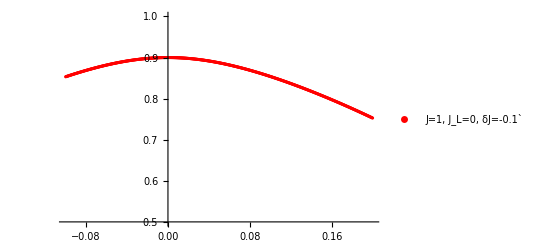

```mathematica
A = ListPlot[l[[2]],PlotStyle->{Red},PlotRange->{0.5,1},PlotLegends->{"J=1, J_L=0, δJ=-0.1`"}]
```

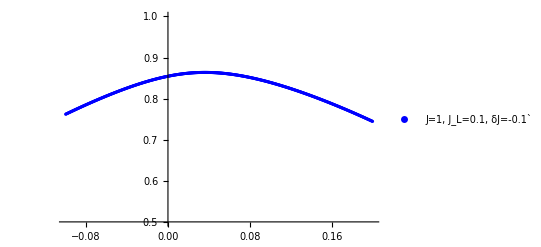

```mathematica
B = ListPlot[l[[4]],PlotLegends->{"J=1, J_L=0.1, δJ=-0.1`"},PlotStyle->{Blue},PlotRange->{0.5,1},PlotLegends->"a"]
```

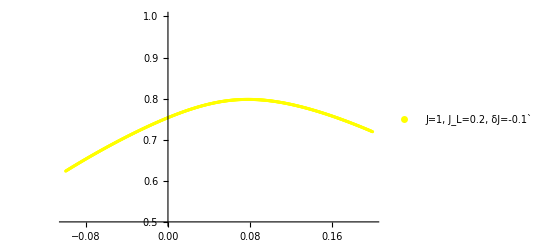

```mathematica
DD = ListPlot[l[[6]],PlotStyle->{Yellow},PlotRange->{0.5,1},PlotLegends->{"J=1, J_L=0.2, δJ=-0.1`"}]
```

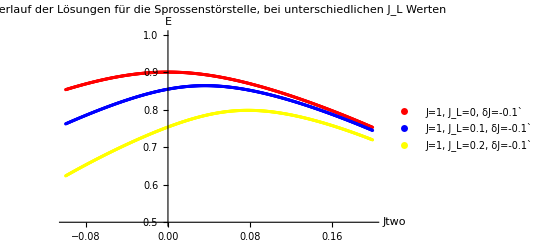

```mathematica
Show[A,B,DD,AxesLabel->{Jtwo,"E"},PlotLabel->"Verlauf der Lösungen für die Sprossenstörstelle, bei unterschiedlichen J_L Werten"]
```

Jetzt das ganze für Jone

```mathematica
ListerJone[Plusminus_,Xstart_,StartIteration_,Jtwoo_,p_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,Jtwoo,p,z],{z,StartIteration}]}}},
Do[
Jonee=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jonee,Jtwoo,p,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{Jonee,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
VerlaufJone[HowMany_,p_] := Module[{lst={}},
For[i=0,i<HowMany,i++,
AppendTo[lst,{1,i*0.02,p}];
AppendTo[lst,Fueger[moduler[ListerJone[-1,-0.0005,Zero[1,0,2*p],i*0.02,p]],moduler[ListerJone[1,0.0005,Zero[1,0,2*p],i*0.02,p]]]]
];
ll = lst
]
```

```mathematica
VerlaufJone[4,-0.1]
```

{{1,0.,-0.1},{{-0.0005,0.899999},{-0.001,0.899995},{-0.0015,0.899988},{-0.002,0.899979},{-0.0025,0.899967},{-0.003,0.899953},{-0.0035,0.899936},{-0.004,0.899916},{-0.0045,0.899893},{-0.005,0.899868},{-0.0055,0.899841},{-0.006,0.899811},{-0.0065,0.899778},{-0.007,0.899742},{-0.0075,0.899704},{-0.008,0.899664},{-0.0085,0.89962},{-0.009,0.899574},{-0.0095,0.899526},{-0.01,0.899475},{-0.0105,0.899421},{-0.011,0.899365},{-0.0115,0.899306},{-0.012,0.899244},{-0.0125,0.89918},{-0.013,0.899113},{-0.0135,0.899044},{-0.014,0.898972},{-0.0145,0.898898},{-0.015,0.898821},{-0.0155,0.898741},{-0.016,0.898659},{-0.0165,0.898575},{-0.017,0.898487},{-0.0175,0.898398},{-0.018,0.898305},{-0.0185,0.89821},{-0.019,0.898113},{-0.0195,0.898013},{-0.02,0.897911},{-0.0205,0.897806},{-0.021,0.897698},{-0.0215,0.897588},{-0.022,0.897476},{-0.0225,0.897361},{-0.023,0.897243},{-0.0235,0.897124},{-0.024,0.897001},{-0.0245,0.896876},{-0.025,0.896749},{-0.0255,0.896619},{-0.026,0.896487},{-0.0265,0.896352},{-0.027,0.896215},{-0.0275,0.896076},{-0.028,0.895934},{-0.0285,0.895789},{-0.029,0.895643},{-0.0295,0.895494},{-0.03,0.895342},{-0.0305,0.895188},{-0.031,0.895032},{-0.0315,0.894873},{-0.032,0.894712},{-0.0325,0.894549},{-0.033,0.894383},{-0.0335,0.894215},{-0.034,0.894044},{-0.0345,0.893872},{-0.035,0.893697},{-0.0355,0.893519},{-0.036,0.89334},{-0.0365,0.893158},{-0.037,0.892974},{-0.0375,0.892787},{-0.038,0.892598},{-0.0385,0.892407},{-0.039,0.892214},{-0.0395,0.892019},{-0.04,0.891821},{-0.0405,0.891621},{-0.041,0.891419},{-0.0415,0.891214},{-0.042,0.891008},{-0.0425,0.890799},{-0.043,0.890588},{-0.0435,0.890375},{-0.044,0.89016},{-0.0445,0.889943},{-0.045,0.889723},{-0.0455,0.889501},{-0.046,0.889278},{-0.0465,0.889052},{-0.047,0.888824},{-0.0475,0.888594},{-0.048,0.888361},{-0.0485,0.888127},{-0.049,0.887891},{-0.0495,0.887652},{-0.05,0.887412},{-0.0505,0.887169},{-0.051,0.886925},{-0.0515,0.886678},{-0.052,0.88643},{-0.0525,0.886179},{-0.053,0.885927},{-0.0535,0.885672},{-0.054,0.885416},{-0.0545,0.885157},{-0.055,0.884897},{-0.0555,0.884634},{-0.056,0.88437},{-0.0565,0.884104},{-0.057,0.883835},{-0.0575,0.883565},{-0.058,0.883293},{-0.0585,0.883019},{-0.059,0.882743},{-0.0595,0.882466},{-0.06,0.882186},{-0.0605,0.881905},{-0.061,0.881621},{-0.0615,0.881336},{-0.062,0.881049},{-0.0625,0.880761},{-0.063,0.88047},{-0.0635,0.880178},{-0.064,0.879883},{-0.0645,0.879587},{-0.065,0.87929},{-0.0655,0.87899},{-0.066,0.878689},{-0.0665,0.878386},{-0.067,0.878081},{-0.0675,0.877774},{-0.068,0.877466},{-0.0685,0.877156},{-0.069,0.876844},{-0.0695,0.876531},{-0.07,0.876216},{-0.0705,0.875899},{-0.071,0.87558},{-0.0715,0.87526},{-0.072,0.874938},{-0.0725,0.874615},{-0.073,0.87429},{-0.0735,0.873963},{-0.074,0.873635},{-0.0745,0.873305},{-0.075,0.872973},{-0.0755,0.87264},{-0.076,0.872305},{-0.0765,0.871968},{-0.077,0.87163},{-0.0775,0.871291},{-0.078,0.87095},{-0.0785,0.870607},{-0.079,0.870263},{-0.0795,0.869917},{-0.08,0.86957},{-0.0805,0.869221},{-0.081,0.86887},{-0.0815,0.868518},{-0.082,0.868165},{-0.0825,0.86781},{-0.083,0.867454},{-0.0835,0.867096},{-0.084,0.866737},{-0.0845,0.866376},{-0.085,0.866014},{-0.0855,0.86565},{-0.086,0.865285},{-0.0865,0.864918},{-0.087,0.86455},{-0.0875,0.864181},{-0.088,0.86381},{-0.0885,0.863437},{-0.089,0.863064},{-0.0895,0.862689},{-0.09,0.862312},{-0.0905,0.861934},{-0.091,0.861555},{-0.0915,0.861174},{-0.092,0.860792},{-0.0925,0.860409},{-0.093,0.860024},{-0.0935,0.859638},{-0.094,0.859251},{-0.0945,0.858862},{-0.095,0.858472},{-0.0955,0.858081},{-0.096,0.857688},{-0.0965,0.857294},{-0.097,0.856899},{-0.0975,0.856502},{-0.098,0.856104},{-0.0985,0.855705},{-0.099,0.855305},{-0.0995,0.854903},{-0.1,0.8545},{0.0005,0.899999},{0.001,0.899995},{0.0015,0.899988},{0.002,0.899979},{0.0025,0.899967},{0.003,0.899953},{0.0035,0.899936},{0.004,0.899916},{0.0045,0.899893},{0.005,0.899868},{0.0055,0.899841},{0.006,0.899811},{0.0065,0.899778},{0.007,0.899742},{0.0075,0.899704},{0.008,0.899664},{0.0085,0.89962},{0.009,0.899574},{0.0095,0.899526},{0.01,0.899475},{0.0105,0.899421},{0.011,0.899365},{0.0115,0.899306},{0.012,0.899244},{0.0125,0.89918},{0.013,0.899113},{0.0135,0.899044},{0.014,0.898972},{0.0145,0.898898},{0.015,0.898821},{0.0155,0.898741},{0.016,0.898659},{0.0165,0.898575},{0.017,0.898487},{0.0175,0.898398},{0.018,0.898305},{0.0185,0.89821},{0.019,0.898113},{0.0195,0.898013},{0.02,0.897911},{0.0205,0.897806},{0.021,0.897698},{0.0215,0.897588},{0.022,0.897476},{0.0225,0.897361},{0.023,0.897243},{0.0235,0.897124},{0.024,0.897001},{0.0245,0.896876},{0.025,0.896749},{0.0255,0.896619},{0.026,0.896487},{0.0265,0.896352},{0.027,0.896215},{0.0275,0.896076},{0.028,0.895934},{0.0285,0.895789},{0.029,0.895643},{0.0295,0.895494},{0.03,0.895342},{0.0305,0.895188},{0.031,0.895032},{0.0315,0.894873},{0.032,0.894712},{0.0325,0.894549},{0.033,0.894383},{0.0335,0.894215},{0.034,0.894044},{0.0345,0.893872},{0.035,0.893697},{0.0355,0.893519},{0.036,0.89334},{0.0365,0.893158},{0.037,0.892974},{0.0375,0.892787},{0.038,0.892598},{0.0385,0.892407},{0.039,0.892214},{0.0395,0.892019},{0.04,0.891821},{0.0405,0.891621},{0.041,0.891419},{0.0415,0.891214},{0.042,0.891008},{0.0425,0.890799},{0.043,0.890588},{0.0435,0.890375},{0.044,0.89016},{0.0445,0.889943},{0.045,0.889723},{0.0455,0.889501},{0.046,0.889278},{0.0465,0.889052},{0.047,0.888824},{0.0475,0.888594},{0.048,0.888361},{0.0485,0.888127},{0.049,0.887891},{0.0495,0.887652},{0.05,0.887412},{0.0505,0.887169},{0.051,0.886925},{0.0515,0.886678},{0.052,0.88643},{0.0525,0.886179},{0.053,0.885927},{0.0535,0.885672},{0.054,0.885416},{0.0545,0.885157},{0.055,0.884897},{0.0555,0.884634},{0.056,0.88437},{0.0565,0.884104},{0.057,0.883835},{0.0575,0.883565},{0.058,0.883293},{0.0585,0.883019},{0.059,0.882743},{0.0595,0.882466},{0.06,0.882186},{0.0605,0.881905},{0.061,0.881621},{0.0615,0.881336},{0.062,0.881049},{0.0625,0.880761},{0.063,0.88047},{0.0635,0.880178},{0.064,0.879883},{0.0645,0.879587},{0.065,0.87929},{0.0655,0.87899},{0.066,0.878689},{0.0665,0.878386},{0.067,0.878081},{0.0675,0.877774},{0.068,0.877466},{0.0685,0.877156},{0.069,0.876844},{0.0695,0.876531},{0.07,0.876216},{0.0705,0.875899},{0.071,0.87558},{0.0715,0.87526},{0.072,0.874938},{0.0725,0.874615},{0.073,0.87429},{0.0735,0.873963},{0.074,0.873635},{0.0745,0.873305},{0.075,0.872973},{0.0755,0.87264},{0.076,0.872305},{0.0765,0.871968},{0.077,0.87163},{0.0775,0.871291},{0.078,0.87095},{0.0785,0.870607},{0.079,0.870263},{0.0795,0.869917},{0.08,0.86957},{0.0805,0.869221},{0.081,0.86887},{0.0815,0.868518},{0.082,0.868165},{0.0825,0.86781},{0.083,0.867454},{0.0835,0.867096},{0.084,0.866737},{0.0845,0.866376},{0.085,0.866014},{0.0855,0.86565},{0.086,0.865285},{0.0865,0.864918},{0.087,0.86455},{0.0875,0.864181},{0.088,0.86381},{0.0885,0.863437},{0.089,0.863064},{0.0895,0.862689},{0.09,0.862312},{0.0905,0.861934},{0.091,0.861555},{0.0915,0.861174},{0.092,0.860792},{0.0925,0.860409},{0.093,0.860024},{0.0935,0.859638},{0.094,0.859251},{0.0945,0.858862},{0.095,0.858472},{0.0955,0.858081},{0.096,0.857688},{0.0965,0.857294},{0.097,0.856899},{0.0975,0.856502},{0.098,0.856104},{0.0985,0.855705},{0.099,0.855305},{0.0995,0.854903},{0.1,0.8545}},{1,0.1,-0.1},{{-0.0005,0.897868},{-0.001,0.897866},{-0.0015,0.897861},{-0.002,0.897854},{-0.0025,0.897845},{-0.003,0.897835},{-0.0035,0.897822},{-0.004,0.897808},{-0.0045,0.897792},{-0.005,0.897773},{-0.0055,0.897753},{-0.006,0.897731},{-0.0065,0.897707},{-0.007,0.897681},{-0.0075,0.897653},{-0.008,0.897623},{-0.0085,0.897592},{-0.009,0.897558},{-0.0095,0.897523},{-0.01,0.897485},{-0.0105,0.897446},{-0.011,0.897405},{-0.0115,0.897362},{-0.012,0.897316},{-0.0125,0.897269},{-0.013,0.897221},{-0.0135,0.89717},{-0.014,0.897117},{-0.0145,0.897062},{-0.015,0.897006},{-0.0155,0.896948},{-0.016,0.896887},{-0.0165,0.896825},{-0.017,0.896761},{-0.0175,0.896695},{-0.018,0.896627},{-0.0185,0.896557},{-0.019,0.896486},{-0.0195,0.896412},{-0.02,0.896336},{-0.0205,0.896259},{-0.021,0.89618},{-0.0215,0.896099},{-0.022,0.896016},{-0.0225,0.895931},{-0.023,0.895844},{-0.0235,0.895755},{-0.024,0.895665},{-0.0245,0.895573},{-0.025,0.895478},{-0.0255,0.895382},{-0.026,0.895284},{-0.0265,0.895184},{-0.027,0.895083},{-0.0275,0.894979},{-0.028,0.894874},{-0.0285,0.894766},{-0.029,0.894657},{-0.0295,0.894546},{-0.03,0.894433},{-0.0305,0.894319},{-0.031,0.894202},{-0.0315,0.894084},{-0.032,0.893964},{-0.0325,0.893842},{-0.033,0.893718},{-0.0335,0.893592},{-0.034,0.893464},{-0.0345,0.893335},{-0.035,0.893204},{-0.0355,0.893071},{-0.036,0.892936},{-0.0365,0.8928},{-0.037,0.892661},{-0.0375,0.892521},{-0.038,0.892379},{-0.0385,0.892235},{-0.039,0.892089},{-0.0395,0.891942},{-0.04,0.891793},{-0.0405,0.891642},{-0.041,0.891489},{-0.0415,0.891334},{-0.042,0.891178},{-0.0425,0.89102},{-0.043,0.89086},{-0.0435,0.890698},{-0.044,0.890535},{-0.0445,0.890369},{-0.045,0.890203},{-0.0455,0.890034},{-0.046,0.889863},{-0.0465,0.889691},{-0.047,0.889517},{-0.0475,0.889341},{-0.048,0.889164},{-0.0485,0.888985},{-0.049,0.888804},{-0.0495,0.888621},{-0.05,0.888437},{-0.0505,0.888251},{-0.051,0.888063},{-0.0515,0.887873},{-0.052,0.887682},{-0.0525,0.887489},{-0.053,0.887294},{-0.0535,0.887098},{-0.054,0.8869},{-0.0545,0.8867},{-0.055,0.886499},{-0.0555,0.886295},{-0.056,0.886091},{-0.0565,0.885884},{-0.057,0.885676},{-0.0575,0.885466},{-0.058,0.885255},{-0.0585,0.885041},{-0.059,0.884827},{-0.0595,0.88461},{-0.06,0.884392},{-0.0605,0.884172},{-0.061,0.883951},{-0.0615,0.883728},{-0.062,0.883503},{-0.0625,0.883277},{-0.063,0.883049},{-0.0635,0.882819},{-0.064,0.882588},{-0.0645,0.882355},{-0.065,0.882121},{-0.0655,0.881885},{-0.066,0.881647},{-0.0665,0.881408},{-0.067,0.881167},{-0.0675,0.880925},{-0.068,0.880681},{-0.0685,0.880435},{-0.069,0.880188},{-0.0695,0.879939},{-0.07,0.879689},{-0.0705,0.879437},{-0.071,0.879183},{-0.0715,0.878928},{-0.072,0.878672},{-0.0725,0.878414},{-0.073,0.878154},{-0.0735,0.877893},{-0.074,0.87763},{-0.0745,0.877366},{-0.075,0.8771},{-0.0755,0.876833},{-0.076,0.876564},{-0.0765,0.876294},{-0.077,0.876022},{-0.0775,0.875749},{-0.078,0.875474},{-0.0785,0.875197},{-0.079,0.874919},{-0.0795,0.87464},{-0.08,0.874359},{-0.0805,0.874077},{-0.081,0.873793},{-0.0815,0.873508},{-0.082,0.873221},{-0.0825,0.872933},{-0.083,0.872643},{-0.0835,0.872352},{-0.084,0.872059},{-0.0845,0.871765},{-0.085,0.87147},{-0.0855,0.871173},{-0.086,0.870875},{-0.0865,0.870575},{-0.087,0.870273},{-0.0875,0.869971},{-0.088,0.869667},{-0.0885,0.869361},{-0.089,0.869054},{-0.0895,0.868746},{-0.09,0.868436},{-0.0905,0.868125},{-0.091,0.867813},{-0.0915,0.867499},{-0.092,0.867183},{-0.0925,0.866867},{-0.093,0.866549},{-0.0935,0.866229},{-0.094,0.865908},{-0.0945,0.865586},{-0.095,0.865263},{-0.0955,0.864938},{-0.096,0.864612},{-0.0965,0.864284},{-0.097,0.863955},{-0.0975,0.863625},{-0.098,0.863293},{-0.0985,0.86296},{-0.099,0.862626},{-0.0995,0.86229},{-0.1,0.861953},{0.0005,0.897868},{0.001,0.897866},{0.0015,0.897861},{0.002,0.897854},{0.0025,0.897845},{0.003,0.897835},{0.0035,0.897822},{0.004,0.897808},{0.0045,0.897792},{0.005,0.897773},{0.0055,0.897753},{0.006,0.897731},{0.0065,0.897707},{0.007,0.897681},{0.0075,0.897653},{0.008,0.897623},{0.0085,0.897592},{0.009,0.897558},{0.0095,0.897523},{0.01,0.897485},{0.0105,0.897446},{0.011,0.897405},{0.0115,0.897362},{0.012,0.897316},{0.0125,0.897269},{0.013,0.897221},{0.0135,0.89717},{0.014,0.897117},{0.0145,0.897062},{0.015,0.897006},{0.0155,0.896948},{0.016,0.896887},{0.0165,0.896825},{0.017,0.896761},{0.0175,0.896695},{0.018,0.896627},{0.0185,0.896557},{0.019,0.896486},{0.0195,0.896412},{0.02,0.896336},{0.0205,0.896259},{0.021,0.89618},{0.0215,0.896099},{0.022,0.896016},{0.0225,0.895931},{0.023,0.895844},{0.0235,0.895755},{0.024,0.895665},{0.0245,0.895573},{0.025,0.895478},{0.0255,0.895382},{0.026,0.895284},{0.0265,0.895184},{0.027,0.895083},{0.0275,0.894979},{0.028,0.894874},{0.0285,0.894766},{0.029,0.894657},{0.0295,0.894546},{0.03,0.894433},{0.0305,0.894319},{0.031,0.894202},{0.0315,0.894084},{0.032,0.893964},{0.0325,0.893842},{0.033,0.893718},{0.0335,0.893592},{0.034,0.893464},{0.0345,0.893335},{0.035,0.893204},{0.0355,0.893071},{0.036,0.892936},{0.0365,0.8928},{0.037,0.892661},{0.0375,0.892521},{0.038,0.892379},{0.0385,0.892235},{0.039,0.892089},{0.0395,0.891942},{0.04,0.891793},{0.0405,0.891642},{0.041,0.891489},{0.0415,0.891334},{0.042,0.891178},{0.0425,0.89102},{0.043,0.89086},{0.0435,0.890698},{0.044,0.890535},{0.0445,0.890369},{0.045,0.890203},{0.0455,0.890034},{0.046,0.889863},{0.0465,0.889691},{0.047,0.889517},{0.0475,0.889341},{0.048,0.889164},{0.0485,0.888985},{0.049,0.888804},{0.0495,0.888621},{0.05,0.888437},{0.0505,0.888251},{0.051,0.888063},{0.0515,0.887873},{0.052,0.887682},{0.0525,0.887489},{0.053,0.887294},{0.0535,0.887098},{0.054,0.8869},{0.0545,0.8867},{0.055,0.886499},{0.0555,0.886295},{0.056,0.886091},{0.0565,0.885884},{0.057,0.885676},{0.0575,0.885466},{0.058,0.885255},{0.0585,0.885041},{0.059,0.884827},{0.0595,0.88461},{0.06,0.884392},{0.0605,0.884172},{0.061,0.883951},{0.0615,0.883728},{0.062,0.883503},{0.0625,0.883277},{0.063,0.883049},{0.0635,0.882819},{0.064,0.882588},{0.0645,0.882355},{0.065,0.882121},{0.0655,0.881885},{0.066,0.881647},{0.0665,0.881408},{0.067,0.881167},{0.0675,0.880925},{0.068,0.880681},{0.0685,0.880435},{0.069,0.880188},{0.0695,0.879939},{0.07,0.879689},{0.0705,0.879437},{0.071,0.879183},{0.0715,0.878928},{0.072,0.878672},{0.0725,0.878414},{0.073,0.878154},{0.0735,0.877893},{0.074,0.87763},{0.0745,0.877366},{0.075,0.8771},{0.0755,0.876833},{0.076,0.876564},{0.0765,0.876294},{0.077,0.876022},{0.0775,0.875749},{0.078,0.875474},{0.0785,0.875197},{0.079,0.874919},{0.0795,0.87464},{0.08,0.874359},{0.0805,0.874077},{0.081,0.873793},{0.0815,0.873508},{0.082,0.873221},{0.0825,0.872933},{0.083,0.872643},{0.0835,0.872352},{0.084,0.872059},{0.0845,0.871765},{0.085,0.87147},{0.0855,0.871173},{0.086,0.870875},{0.0865,0.870575},{0.087,0.870273},{0.0875,0.869971},{0.088,0.869667},{0.0885,0.869361},{0.089,0.869054},{0.0895,0.868746},{0.09,0.868436},{0.0905,0.868125},{0.091,0.867813},{0.0915,0.867499},{0.092,0.867183},{0.0925,0.866867},{0.093,0.866549},{0.0935,0.866229},{0.094,0.865908},{0.0945,0.865586},{0.095,0.865263},{0.0955,0.864938},{0.096,0.864612},{0.0965,0.864284},{0.097,0.863955},{0.0975,0.863625},{0.098,0.863293},{0.0985,0.86296},{0.099,0.862626},{0.0995,0.86229},{0.1,0.861953}},{1,0.2,-0.1},{{-0.0005,0.89168},{-0.001,0.891677},{-0.0015,0.891674},{-0.002,0.891669},{-0.0025,0.891662},{-0.003,0.891655},{-0.0035,0.891645},{-0.004,0.891634},{-0.0045,0.891622},{-0.005,0.891609},{-0.0055,0.891594},{-0.006,0.891577},{-0.0065,0.891559},{-0.007,0.89154},{-0.0075,0.891519},{-0.008,0.891497},{-0.0085,0.891474},{-0.009,0.891449},{-0.0095,0.891422},{-0.01,0.891394},{-0.0105,0.891365},{-0.011,0.891334},{-0.0115,0.891302},{-0.012,0.891268},{-0.0125,0.891233},{-0.013,0.891197},{-0.0135,0.891159},{-0.014,0.89112},{-0.0145,0.891079},{-0.015,0.891037},{-0.0155,0.890993},{-0.016,0.890948},{-0.0165,0.890902},{-0.017,0.890854},{-0.0175,0.890805},{-0.018,0.890754},{-0.0185,0.890702},{-0.019,0.890648},{-0.0195,0.890593},{-0.02,0.890537},{-0.0205,0.890479},{-0.021,0.89042},{-0.0215,0.890359},{-0.022,0.890297},{-0.0225,0.890233},{-0.023,0.890168},{-0.0235,0.890102},{-0.024,0.890034},{-0.0245,0.889965},{-0.025,0.889894},{-0.0255,0.889822},{-0.026,0.889749},{-0.0265,0.889674},{-0.027,0.889598},{-0.0275,0.88952},{-0.028,0.889441},{-0.0285,0.88936},{-0.029,0.889278},{-0.0295,0.889195},{-0.03,0.88911},{-0.0305,0.889024},{-0.031,0.888937},{-0.0315,0.888848},{-0.032,0.888757},{-0.0325,0.888665},{-0.033,0.888572},{-0.0335,0.888477},{-0.034,0.888381},{-0.0345,0.888284},{-0.035,0.888185},{-0.0355,0.888085},{-0.036,0.887983},{-0.0365,0.88788},{-0.037,0.887776},{-0.0375,0.88767},{-0.038,0.887562},{-0.0385,0.887454},{-0.039,0.887344},{-0.0395,0.887232},{-0.04,0.887119},{-0.0405,0.887005},{-0.041,0.886889},{-0.0415,0.886772},{-0.042,0.886654},{-0.0425,0.886534},{-0.043,0.886413},{-0.0435,0.88629},{-0.044,0.886166},{-0.0445,0.886041},{-0.045,0.885914},{-0.0455,0.885786},{-0.046,0.885656},{-0.0465,0.885525},{-0.047,0.885393},{-0.0475,0.885259},{-0.048,0.885124},{-0.0485,0.884987},{-0.049,0.884849},{-0.0495,0.88471},{-0.05,0.884569},{-0.0505,0.884427},{-0.051,0.884284},{-0.0515,0.884139},{-0.052,0.883993},{-0.0525,0.883845},{-0.053,0.883696},{-0.0535,0.883546},{-0.054,0.883394},{-0.0545,0.883241},{-0.055,0.883087},{-0.0555,0.882931},{-0.056,0.882774},{-0.0565,0.882615},{-0.057,0.882456},{-0.0575,0.882294},{-0.058,0.882132},{-0.0585,0.881968},{-0.059,0.881802},{-0.0595,0.881636},{-0.06,0.881468},{-0.0605,0.881298},{-0.061,0.881128},{-0.0615,0.880955},{-0.062,0.880782},{-0.0625,0.880607},{-0.063,0.880431},{-0.0635,0.880253},{-0.064,0.880075},{-0.0645,0.879894},{-0.065,0.879713},{-0.0655,0.87953},{-0.066,0.879346},{-0.0665,0.87916},{-0.067,0.878973},{-0.0675,0.878785},{-0.068,0.878595},{-0.0685,0.878404},{-0.069,0.878212},{-0.0695,0.878018},{-0.07,0.877823},{-0.0705,0.877627},{-0.071,0.877429},{-0.0715,0.87723},{-0.072,0.87703},{-0.0725,0.876829},{-0.073,0.876626},{-0.0735,0.876421},{-0.074,0.876216},{-0.0745,0.876009},{-0.075,0.875801},{-0.0755,0.875591},{-0.076,0.87538},{-0.0765,0.875168},{-0.077,0.874955},{-0.0775,0.87474},{-0.078,0.874524},{-0.0785,0.874306},{-0.079,0.874088},{-0.0795,0.873868},{-0.08,0.873646},{-0.0805,0.873424},{-0.081,0.8732},{-0.0815,0.872974},{-0.082,0.872748},{-0.0825,0.87252},{-0.083,0.872291},{-0.0835,0.87206},{-0.084,0.871829},{-0.0845,0.871596},{-0.085,0.871361},{-0.0855,0.871126},{-0.086,0.870889},{-0.0865,0.870651},{-0.087,0.870411},{-0.0875,0.870171},{-0.088,0.869929},{-0.0885,0.869685},{-0.089,0.869441},{-0.0895,0.869195},{-0.09,0.868948},{-0.0905,0.868699},{-0.091,0.86845},{-0.0915,0.868199},{-0.092,0.867947},{-0.0925,0.867693},{-0.093,0.867438},{-0.0935,0.867182},{-0.094,0.866925},{-0.0945,0.866667},{-0.095,0.866407},{-0.0955,0.866146},{-0.096,0.865884},{-0.0965,0.86562},{-0.097,0.865355},{-0.0975,0.865089},{-0.098,0.864822},{-0.0985,0.864554},{-0.099,0.864284},{-0.0995,0.864013},{-0.1,0.863741},{0.0005,0.89168},{0.001,0.891677},{0.0015,0.891674},{0.002,0.891669},{0.0025,0.891662},{0.003,0.891655},{0.0035,0.891645},{0.004,0.891634},{0.0045,0.891622},{0.005,0.891609},{0.0055,0.891594},{0.006,0.891577},{0.0065,0.891559},{0.007,0.89154},{0.0075,0.891519},{0.008,0.891497},{0.0085,0.891474},{0.009,0.891449},{0.0095,0.891422},{0.01,0.891394},{0.0105,0.891365},{0.011,0.891334},{0.0115,0.891302},{0.012,0.891268},{0.0125,0.891233},{0.013,0.891197},{0.0135,0.891159},{0.014,0.89112},{0.0145,0.891079},{0.015,0.891037},{0.0155,0.890993},{0.016,0.890948},{0.0165,0.890902},{0.017,0.890854},{0.0175,0.890805},{0.018,0.890754},{0.0185,0.890702},{0.019,0.890648},{0.0195,0.890593},{0.02,0.890537},{0.0205,0.890479},{0.021,0.89042},{0.0215,0.890359},{0.022,0.890297},{0.0225,0.890233},{0.023,0.890168},{0.0235,0.890102},{0.024,0.890034},{0.0245,0.889965},{0.025,0.889894},{0.0255,0.889822},{0.026,0.889749},{0.0265,0.889674},{0.027,0.889598},{0.0275,0.88952},{0.028,0.889441},{0.0285,0.88936},{0.029,0.889278},{0.0295,0.889195},{0.03,0.88911},{0.0305,0.889024},{0.031,0.888937},{0.0315,0.888848},{0.032,0.888757},{0.0325,0.888665},{0.033,0.888572},{0.0335,0.888477},{0.034,0.888381},{0.0345,0.888284},{0.035,0.888185},{0.0355,0.888085},{0.036,0.887983},{0.0365,0.88788},{0.037,0.887776},{0.0375,0.88767},{0.038,0.887562},{0.0385,0.887454},{0.039,0.887344},{0.0395,0.887232},{0.04,0.887119},{0.0405,0.887005},{0.041,0.886889},{0.0415,0.886772},{0.042,0.886654},{0.0425,0.886534},{0.043,0.886413},{0.0435,0.88629},{0.044,0.886166},{0.0445,0.886041},{0.045,0.885914},{0.0455,0.885786},{0.046,0.885656},{0.0465,0.885525},{0.047,0.885393},{0.0475,0.885259},{0.048,0.885124},{0.0485,0.884987},{0.049,0.884849},{0.0495,0.88471},{0.05,0.884569},{0.0505,0.884427},{0.051,0.884284},{0.0515,0.884139},{0.052,0.883993},{0.0525,0.883845},{0.053,0.883696},{0.0535,0.883546},{0.054,0.883394},{0.0545,0.883241},{0.055,0.883087},{0.0555,0.882931},{0.056,0.882774},{0.0565,0.882615},{0.057,0.882456},{0.0575,0.882294},{0.058,0.882132},{0.0585,0.881968},{0.059,0.881802},{0.0595,0.881636},{0.06,0.881468},{0.0605,0.881298},{0.061,0.881128},{0.0615,0.880955},{0.062,0.880782},{0.0625,0.880607},{0.063,0.880431},{0.0635,0.880253},{0.064,0.880075},{0.0645,0.879894},{0.065,0.879713},{0.0655,0.87953},{0.066,0.879346},{0.0665,0.87916},{0.067,0.878973},{0.0675,0.878785},{0.068,0.878595},{0.0685,0.878404},{0.069,0.878212},{0.0695,0.878018},{0.07,0.877823},{0.0705,0.877627},{0.071,0.877429},{0.0715,0.87723},{0.072,0.87703},{0.0725,0.876829},{0.073,0.876626},{0.0735,0.876421},{0.074,0.876216},{0.0745,0.876009},{0.075,0.875801},{0.0755,0.875591},{0.076,0.87538},{0.0765,0.875168},{0.077,0.874955},{0.0775,0.87474},{0.078,0.874524},{0.0785,0.874306},{0.079,0.874088},{0.0795,0.873868},{0.08,0.873646},{0.0805,0.873424},{0.081,0.8732},{0.0815,0.872974},{0.082,0.872748},{0.0825,0.87252},{0.083,0.872291},{0.0835,0.87206},{0.084,0.871829},{0.0845,0.871596},{0.085,0.871361},{0.0855,0.871126},{0.086,0.870889},{0.0865,0.870651},{0.087,0.870411},{0.0875,0.870171},{0.088,0.869929},{0.0885,0.869685},{0.089,0.869441},{0.0895,0.869195},{0.09,0.868948},{0.0905,0.868699},{0.091,0.86845},{0.0915,0.868199},{0.092,0.867947},{0.0925,0.867693},{0.093,0.867438},{0.0935,0.867182},{0.094,0.866925},{0.0945,0.866667},{0.095,0.866407},{0.0955,0.866146},{0.096,0.865884},{0.0965,0.86562},{0.097,0.865355},{0.0975,0.865089},{0.098,0.864822},{0.0985,0.864554},{0.099,0.864284},{0.0995,0.864013},{0.1,0.863741}},{1,0.3,-0.1},{{-0.0005,0.881922},{-0.001,0.88192},{-0.0015,0.881918},{-0.002,0.881914},{-0.0025,0.881909},{-0.003,0.881903},{-0.0035,0.881896},{-0.004,0.881887},{-0.0045,0.881878},{-0.005,0.881867},{-0.0055,0.881856},{-0.006,0.881843},{-0.0065,0.88183},{-0.007,0.881815},{-0.0075,0.881799},{-0.008,0.881782},{-0.0085,0.881764},{-0.009,0.881744},{-0.0095,0.881724},{-0.01,0.881703},{-0.0105,0.88168},{-0.011,0.881656},{-0.0115,0.881632},{-0.012,0.881606},{-0.0125,0.881579},{-0.013,0.881551},{-0.0135,0.881522},{-0.014,0.881491},{-0.0145,0.88146},{-0.015,0.881428},{-0.0155,0.881394},{-0.016,0.88136},{-0.0165,0.881324},{-0.017,0.881287},{-0.0175,0.881249},{-0.018,0.88121},{-0.0185,0.88117},{-0.019,0.881129},{-0.0195,0.881086},{-0.02,0.881043},{-0.0205,0.880998},{-0.021,0.880953},{-0.0215,0.880906},{-0.022,0.880858},{-0.0225,0.880809},{-0.023,0.880759},{-0.0235,0.880708},{-0.024,0.880656},{-0.0245,0.880603},{-0.025,0.880548},{-0.0255,0.880493},{-0.026,0.880436},{-0.0265,0.880379},{-0.027,0.88032},{-0.0275,0.88026},{-0.028,0.880199},{-0.0285,0.880137},{-0.029,0.880074},{-0.0295,0.880009},{-0.03,0.879944},{-0.0305,0.879877},{-0.031,0.87981},{-0.0315,0.879741},{-0.032,0.879671},{-0.0325,0.879601},{-0.033,0.879529},{-0.0335,0.879456},{-0.034,0.879381},{-0.0345,0.879306},{-0.035,0.87923},{-0.0355,0.879152},{-0.036,0.879074},{-0.0365,0.878994},{-0.037,0.878913},{-0.0375,0.878832},{-0.038,0.878749},{-0.0385,0.878665},{-0.039,0.878579},{-0.0395,0.878493},{-0.04,0.878406},{-0.0405,0.878317},{-0.041,0.878228},{-0.0415,0.878137},{-0.042,0.878046},{-0.0425,0.877953},{-0.043,0.877859},{-0.0435,0.877764},{-0.044,0.877668},{-0.0445,0.877571},{-0.045,0.877472},{-0.0455,0.877373},{-0.046,0.877273},{-0.0465,0.877171},{-0.047,0.877068},{-0.0475,0.876965},{-0.048,0.87686},{-0.0485,0.876754},{-0.049,0.876647},{-0.0495,0.876539},{-0.05,0.87643},{-0.0505,0.876319},{-0.051,0.876208},{-0.0515,0.876095},{-0.052,0.875982},{-0.0525,0.875867},{-0.053,0.875751},{-0.0535,0.875634},{-0.054,0.875516},{-0.0545,0.875397},{-0.055,0.875277},{-0.0555,0.875156},{-0.056,0.875034},{-0.0565,0.87491},{-0.057,0.874786},{-0.0575,0.87466},{-0.058,0.874533},{-0.0585,0.874406},{-0.059,0.874277},{-0.0595,0.874147},{-0.06,0.874016},{-0.0605,0.873884},{-0.061,0.87375},{-0.0615,0.873616},{-0.062,0.873481},{-0.0625,0.873344},{-0.063,0.873207},{-0.0635,0.873068},{-0.064,0.872928},{-0.0645,0.872787},{-0.065,0.872645},{-0.0655,0.872502},{-0.066,0.872358},{-0.0665,0.872213},{-0.067,0.872066},{-0.0675,0.871919},{-0.068,0.871771},{-0.0685,0.871621},{-0.069,0.87147},{-0.0695,0.871319},{-0.07,0.871166},{-0.0705,0.871012},{-0.071,0.870857},{-0.0715,0.870701},{-0.072,0.870543},{-0.0725,0.870385},{-0.073,0.870226},{-0.0735,0.870065},{-0.074,0.869904},{-0.0745,0.869741},{-0.075,0.869578},{-0.0755,0.869413},{-0.076,0.869247},{-0.0765,0.86908},{-0.077,0.868912},{-0.0775,0.868743},{-0.078,0.868573},{-0.0785,0.868401},{-0.079,0.868229},{-0.0795,0.868055},{-0.08,0.867881},{-0.0805,0.867705},{-0.081,0.867528},{-0.0815,0.867351},{-0.082,0.867172},{-0.0825,0.866992},{-0.083,0.866811},{-0.0835,0.866629},{-0.084,0.866446},{-0.0845,0.866261},{-0.085,0.866076},{-0.0855,0.865889},{-0.086,0.865702},{-0.0865,0.865513},{-0.087,0.865324},{-0.0875,0.865133},{-0.088,0.864941},{-0.0885,0.864748},{-0.089,0.864554},{-0.0895,0.864359},{-0.09,0.864163},{-0.0905,0.863966},{-0.091,0.863767},{-0.0915,0.863568},{-0.092,0.863367},{-0.0925,0.863166},{-0.093,0.862963},{-0.0935,0.86276},{-0.094,0.862555},{-0.0945,0.862349},{-0.095,0.862142},{-0.0955,0.861934},{-0.096,0.861725},{-0.0965,0.861515},{-0.097,0.861304},{-0.0975,0.861091},{-0.098,0.860878},{-0.0985,0.860664},{-0.099,0.860448},{-0.0995,0.860232},{-0.1,0.860014},{0.0005,0.881922},{0.001,0.88192},{0.0015,0.881918},{0.002,0.881914},{0.0025,0.881909},{0.003,0.881903},{0.0035,0.881896},{0.004,0.881887},{0.0045,0.881878},{0.005,0.881867},{0.0055,0.881856},{0.006,0.881843},{0.0065,0.88183},{0.007,0.881815},{0.0075,0.881799},{0.008,0.881782},{0.0085,0.881764},{0.009,0.881744},{0.0095,0.881724},{0.01,0.881703},{0.0105,0.88168},{0.011,0.881656},{0.0115,0.881632},{0.012,0.881606},{0.0125,0.881579},{0.013,0.881551},{0.0135,0.881522},{0.014,0.881491},{0.0145,0.88146},{0.015,0.881428},{0.0155,0.881394},{0.016,0.88136},{0.0165,0.881324},{0.017,0.881287},{0.0175,0.881249},{0.018,0.88121},{0.0185,0.88117},{0.019,0.881129},{0.0195,0.881086},{0.02,0.881043},{0.0205,0.880998},{0.021,0.880953},{0.0215,0.880906},{0.022,0.880858},{0.0225,0.880809},{0.023,0.880759},{0.0235,0.880708},{0.024,0.880656},{0.0245,0.880603},{0.025,0.880548},{0.0255,0.880493},{0.026,0.880436},{0.0265,0.880379},{0.027,0.88032},{0.0275,0.88026},{0.028,0.880199},{0.0285,0.880137},{0.029,0.880074},{0.0295,0.880009},{0.03,0.879944},{0.0305,0.879877},{0.031,0.87981},{0.0315,0.879741},{0.032,0.879671},{0.0325,0.879601},{0.033,0.879529},{0.0335,0.879456},{0.034,0.879381},{0.0345,0.879306},{0.035,0.87923},{0.0355,0.879152},{0.036,0.879074},{0.0365,0.878994},{0.037,0.878913},{0.0375,0.878832},{0.038,0.878749},{0.0385,0.878665},{0.039,0.878579},{0.0395,0.878493},{0.04,0.878406},{0.0405,0.878317},{0.041,0.878228},{0.0415,0.878137},{0.042,0.878046},{0.0425,0.877953},{0.043,0.877859},{0.0435,0.877764},{0.044,0.877668},{0.0445,0.877571},{0.045,0.877472},{0.0455,0.877373},{0.046,0.877273},{0.0465,0.877171},{0.047,0.877068},{0.0475,0.876965},{0.048,0.87686},{0.0485,0.876754},{0.049,0.876647},{0.0495,0.876539},{0.05,0.87643},{0.0505,0.876319},{0.051,0.876208},{0.0515,0.876095},{0.052,0.875982},{0.0525,0.875867},{0.053,0.875751},{0.0535,0.875634},{0.054,0.875516},{0.0545,0.875397},{0.055,0.875277},{0.0555,0.875156},{0.056,0.875034},{0.0565,0.87491},{0.057,0.874786},{0.0575,0.87466},{0.058,0.874533},{0.0585,0.874406},{0.059,0.874277},{0.0595,0.874147},{0.06,0.874016},{0.0605,0.873884},{0.061,0.87375},{0.0615,0.873616},{0.062,0.873481},{0.0625,0.873344},{0.063,0.873207},{0.0635,0.873068},{0.064,0.872928},{0.0645,0.872787},{0.065,0.872645},{0.0655,0.872502},{0.066,0.872358},{0.0665,0.872213},{0.067,0.872066},{0.0675,0.871919},{0.068,0.871771},{0.0685,0.871621},{0.069,0.87147},{0.0695,0.871319},{0.07,0.871166},{0.0705,0.871012},{0.071,0.870857},{0.0715,0.870701},{0.072,0.870543},{0.0725,0.870385},{0.073,0.870226},{0.0735,0.870065},{0.074,0.869904},{0.0745,0.869741},{0.075,0.869578},{0.0755,0.869413},{0.076,0.869247},{0.0765,0.86908},{0.077,0.868912},{0.0775,0.868743},{0.078,0.868573},{0.0785,0.868401},{0.079,0.868229},{0.0795,0.868055},{0.08,0.867881},{0.0805,0.867705},{0.081,0.867528},{0.0815,0.867351},{0.082,0.867172},{0.0825,0.866992},{0.083,0.866811},{0.0835,0.866629},{0.084,0.866446},{0.0845,0.866261},{0.085,0.866076},{0.0855,0.865889},{0.086,0.865702},{0.0865,0.865513},{0.087,0.865324},{0.0875,0.865133},{0.088,0.864941},{0.0885,0.864748},{0.089,0.864554},{0.0895,0.864359},{0.09,0.864163},{0.0905,0.863966},{0.091,0.863767},{0.0915,0.863568},{0.092,0.863367},{0.0925,0.863166},{0.093,0.862963},{0.0935,0.86276},{0.094,0.862555},{0.0945,0.862349},{0.095,0.862142},{0.0955,0.861934},{0.096,0.861725},{0.0965,0.861515},{0.097,0.861304},{0.0975,0.861091},{0.098,0.860878},{0.0985,0.860664},{0.099,0.860448},{0.0995,0.860232},{0.1,0.860014}}}

```mathematica
ll[[7]]
```

{1,0.3,-0.1}

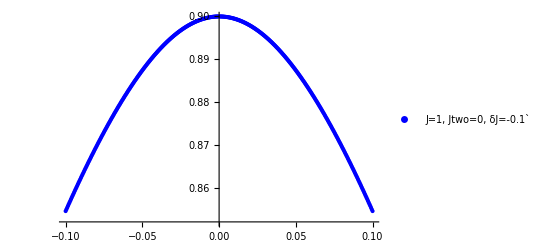

```mathematica
K = ListPlot[ll[[2]],PlotStyle->Blue,PlotLegends->{"J=1, Jtwo=0, δJ=-0.1`"}]
```

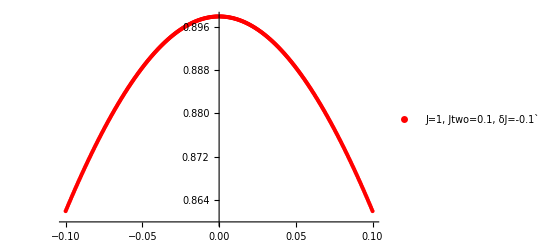

```mathematica
L = ListPlot[ll[[4]],PlotStyle->Red,PlotLegends->{"J=1, Jtwo=0.1, δJ=-0.1`"}]
```

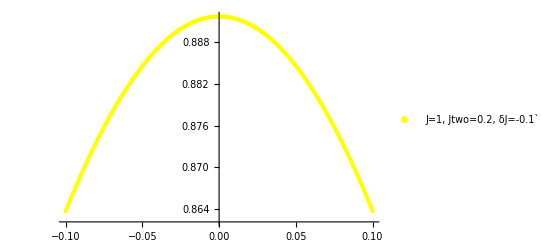

```mathematica
M = ListPlot[ll[[6]],PlotStyle->Yellow,PlotLegends->{"J=1, Jtwo=0.2, δJ=-0.1`"}]
```

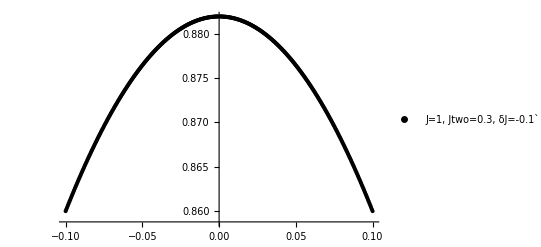

```mathematica
P = ListPlot[ll[[8]],PlotStyle->Black,PlotLegends->{"J=1, Jtwo=0.3, δJ=-0.1`"}]
```

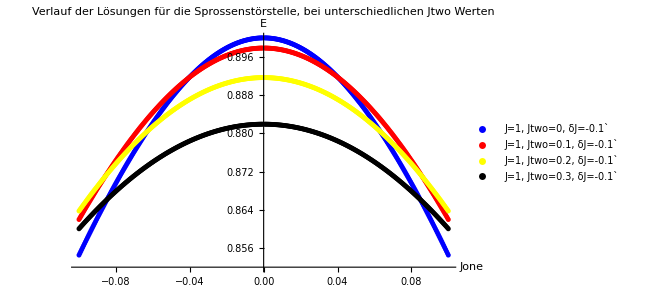

```mathematica
Show[K,L,M,P,AxesLabel->{Jone,"E"},PlotLabel->"Verlauf der Lösungen für die Sprossenstörstelle, bei unterschiedlichen Jtwo Werten"]
```

Und für delta J

```mathematica
ListerdJ[Plusminus_,Xstart_,StartIteration_,Jone_,Jtwoo_] := Module[{lst={{Xstart,FindRoot[Nulls[Jone,Jtwoo,Xstart,z],{z,StartIteration}]}}},
Do[
p=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jone,Jtwoo,p,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{p,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
VerlaufdJJone[HowMany_,Jone_,Jtwo_] := Module[{lst={}},
For[i=0,i<HowMany,i++,
AppendTo[lst,{1,Jone,Jtwo,i*0.1}];
AppendTo[lst,Fueger[moduler[ListerdJ[-1,-0.0005,Zero[1,Jone,2*-0.0005],Jone,Jtwo]],moduler[ListerdJ[1,0.0005,Zero[1,Jone,2*-0.0005],Jone,Jtwo]]]]
];
lll = lst
]
```

```mathematica
VerlaufdJJone[2,0.2,0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.04306}. NIntegrate obtained -0.00170988 and 0.00169442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.04306}. NIntegrate obtained 0.000248801 and 1.03627×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.04306}. NIntegrate obtained -0.0000151176 and 0.000203069 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1,0.2,0.1,0.},{{-0.0005,1.24705},{-0.001,1.24705},{-0.0015,1.24705},{-0.002,1.24705},{-0.0025,1.24705},{-0.003,1.24705},{-0.0035,1.24705},{-0.004,1.24705},{-0.0045,1.24705},{-0.005,1.24705},{-0.0055,1.24705},{-0.006,1.24705},{-0.0065,1.24705},{-0.007,1.24705},{-0.0075,1.24705},{-0.008,1.24705},{-0.0085,1.24705},{-0.009,1.24705},{-0.0095,1.24705},{-0.01,1.24705},{-0.0105,1.24705},{-0.011,1.24705},{-0.0115,1.24705},{-0.012,1.24705},{-0.0125,1.24705},{-0.013,1.24705},{-0.0135,1.24705},{-0.014,1.24705},{-0.0145,1.24705},{-0.015,1.24705},{-0.0155,1.24705},{-0.016,1.24705},{-0.0165,1.24705},{-0.017,1.24705},{-0.0175,1.24705},{-0.018,1.24705},{-0.0185,1.24705},{-0.019,1.24705},{-0.0195,1.24705},{-0.02,1.24705},{-0.0205,1.24705},{-0.021,1.24705},{-0.0215,1.24705},{-0.022,1.24705},{-0.0225,1.24705},{-0.023,1.24705},{-0.0235,1.24705},{-0.024,1.24705},{-0.0245,1.24705},{-0.025,1.24705},{-0.0255,1.24705},{-0.026,1.24705},{-0.0265,1.24705},{-0.027,1.24705},{-0.0275,1.24705},{-0.028,1.24705},{-0.0285,1.24705},{-0.029,1.24705},{-0.0295,1.24705},{-0.03,1.24705},{-0.0305,1.24705},{-0.031,1.24705},{-0.0315,1.24705},{-0.032,1.24705},{-0.0325,1.24705},{-0.033,1.24705},{-0.0335,1.24705},{-0.034,1.24705},{-0.0345,1.24705},{-0.035,1.24705},{-0.0355,1.24705},{-0.036,1.24705},{-0.0365,1.24705},{-0.037,1.24705},{-0.0375,1.24705},{-0.038,1.24705},{-0.0385,1.24705},{-0.039,1.24705},{-0.0395,1.24705},{-0.04,1.24705},{-0.0405,1.24705},{-0.041,1.24705},{-0.0415,1.24705},{-0.042,1.24705},{-0.0425,1.24705},{-0.043,1.24705},{-0.0435,1.24705},{-0.044,1.24705},{-0.0445,1.24705},{-0.045,1.24705},{-0.0455,1.24705},{-0.046,1.24705},{-0.0465,1.24705},{-0.047,1.24705},{-0.0475,1.24705},{-0.048,1.24705},{-0.0485,1.24705},{-0.049,1.24705},{-0.0495,1.24705},{-0.05,1.24705},{-0.0505,1.24705},{-0.051,1.24705},{-0.0515,1.24705},{-0.052,1.24705},{-0.0525,1.24705},{-0.053,1.24705},{-0.0535,1.24705},{-0.054,1.24705},{-0.0545,1.24705},{-0.055,1.24705},{-0.0555,1.24705},{-0.056,1.24705},{-0.0565,1.24705},{-0.057,1.24705},{-0.0575,1.24705},{-0.058,1.24705},{-0.0585,1.24705},{-0.059,1.24705},{-0.0595,1.24705},{-0.06,1.24705},{-0.0605,1.24705},{-0.061,1.24705},{-0.0615,1.24705},{-0.062,1.24705},{-0.0625,1.24705},{-0.063,1.24705},{-0.0635,1.24705},{-0.064,1.24705},{-0.0645,1.24705},{-0.065,1.24705},{-0.0655,1.24705},{-0.066,1.24705},{-0.0665,1.24705},{-0.067,1.24705},{-0.0675,1.24705},{-0.068,1.24705},{-0.0685,1.24705},{-0.069,1.24705},{-0.0695,1.24705},{-0.07,1.24705},{-0.0705,1.24705},{-0.071,1.24705},{-0.0715,1.24705},{-0.072,1.24705},{-0.0725,1.24705},{-0.073,1.24705},{-0.0735,1.24705},{-0.074,1.24705},{-0.0745,1.24705},{-0.075,1.24705},{-0.0755,1.24705},{-0.076,1.24705},{-0.0765,1.24705},{-0.077,1.24705},{-0.0775,1.24705},{-0.078,1.24705},{-0.0785,1.24705},{-0.079,1.24705},{-0.0795,1.24705},{-0.08,1.24705},{-0.0805,1.24705},{-0.081,1.24705},{-0.0815,1.24705},{-0.082,1.24705},{-0.0825,1.24705},{-0.083,1.24705},{-0.0835,1.24705},{-0.084,1.24705},{-0.0845,1.24705},{-0.085,1.24705},{-0.0855,1.24705},{-0.086,1.24705},{-0.0865,1.24705},{-0.087,1.24705},{-0.0875,1.24705},{-0.088,1.24705},{-0.0885,1.24705},{-0.089,1.24705},{-0.0895,1.24705},{-0.09,1.24705},{-0.0905,1.24705},{-0.091,1.24705},{-0.0915,1.24705},{-0.092,1.24705},{-0.0925,1.24705},{-0.093,1.24705},{-0.0935,1.24705},{-0.094,1.24705},{-0.0945,1.24705},{-0.095,1.24705},{-0.0955,1.24705},{-0.096,1.24705},{-0.0965,1.24705},{-0.097,1.24705},{-0.0975,1.24705},{-0.098,1.24705},{-0.0985,1.24705},{-0.099,1.24705},{-0.0995,1.24705},{-0.1,1.24705},{0.0005,-1.26435},{0.001,-1.26435},{0.0015,-1.26435},{0.002,-1.26435},{0.0025,-1.26435},{0.003,-1.26435},{0.0035,-1.26435},{0.004,-1.26435},{0.0045,-1.26435},{0.005,-1.26435},{0.0055,-1.26435},{0.006,-1.26435},{0.0065,-1.26435},{0.007,-1.26435},{0.0075,-1.26435},{0.008,-1.26435},{0.0085,-1.26435},{0.009,-1.26435},{0.0095,-1.26435},{0.01,-1.26435},{0.0105,-1.26435},{0.011,-1.26435},{0.0115,-1.26435},{0.012,-1.26435},{0.0125,-1.26436},{0.013,-1.26436},{0.0135,-1.26436},{0.014,-1.26436},{0.0145,-1.26436},{0.015,-1.26436},{0.0155,-1.26436},{0.016,-1.26436},{0.0165,-1.26436},{0.017,-1.26436},{0.0175,-1.26436},{0.018,-1.26436},{0.0185,-1.26436},{0.019,-1.26436},{0.0195,-1.26436},{0.02,-1.26436},{0.0205,-1.26436},{0.021,-1.26436},{0.0215,-1.26436},{0.022,-1.26436},{0.0225,-1.26436},{0.023,-1.26436},{0.0235,-1.26436},{0.024,-1.26436},{0.0245,-1.26436},{0.025,-1.26436},{0.0255,-1.26436},{0.026,-1.26436},{0.0265,-1.26436},{0.027,-1.26436},{0.0275,-1.26436},{0.028,-1.26436},{0.0285,-1.26436},{0.029,-1.26436},{0.0295,-1.26436},{0.03,-1.26436},{0.0305,-1.26436},{0.031,-1.26436},{0.0315,-1.26436},{0.032,-1.26436},{0.0325,-1.26436},{0.033,-1.26436},{0.0335,-1.26436},{0.034,-1.26436},{0.0345,-1.26436},{0.035,-1.26436},{0.0355,-1.26436},{0.036,-1.26436},{0.0365,-1.26436},{0.037,-1.26436},{0.0375,-1.26436},{0.038,-1.26436},{0.0385,-1.26436},{0.039,-1.26436},{0.0395,-1.26436},{0.04,-1.26436},{0.0405,-1.26436},{0.041,-1.26436},{0.0415,-1.26436},{0.042,-1.26436},{0.0425,-1.26436},{0.043,-1.26436},{0.0435,-1.26436},{0.044,-1.26436},{0.0445,-1.26436},{0.045,-1.26436},{0.0455,-1.26436},{0.046,-1.26436},{0.0465,-1.26436},{0.047,-1.26436},{0.0475,-1.26436},{0.048,-1.26436},{0.0485,-1.26436},{0.049,-1.26436},{0.0495,-1.26436},{0.05,-1.26436},{0.0505,-1.26436},{0.051,-1.26436},{0.0515,-1.26436},{0.052,-1.26436},{0.0525,-1.26436},{0.053,-1.26436},{0.0535,-1.26436},{0.054,-1.26436},{0.0545,-1.26436},{0.055,-1.26436},{0.0555,-1.26436},{0.056,-1.26436},{0.0565,-1.26436},{0.057,-1.26436},{0.0575,-1.26436},{0.058,-1.26436},{0.0585,-1.26436},{0.059,-1.26436},{0.0595,-1.26436},{0.06,-1.26436},{0.0605,-1.26436},{0.061,-1.26436},{0.0615,-1.26436},{0.062,-1.26436},{0.0625,-1.26436},{0.063,-1.26436},{0.0635,-1.26436},{0.064,-1.26436},{0.0645,-1.26436},{0.065,-1.26436},{0.0655,-1.26436},{0.066,-1.26436},{0.0665,-1.26436},{0.067,-1.26436},{0.0675,-1.26436},{0.068,-1.26436},{0.0685,-1.26436},{0.069,-1.26436},{0.0695,-1.26436},{0.07,-1.26436},{0.0705,-1.26436},{0.071,-1.26436},{0.0715,-1.26436},{0.072,-1.26436},{0.0725,-1.26436},{0.073,-1.26436},{0.0735,-1.26436},{0.074,-1.26436},{0.0745,-1.26436},{0.075,-1.26436},{0.0755,-1.26436},{0.076,-1.26436},{0.0765,-1.26436},{0.077,-1.26436},{0.0775,-1.26436},{0.078,-1.26436},{0.0785,-1.26436},{0.079,-1.26436},{0.0795,-1.26436},{0.08,-1.26436},{0.0805,-1.26436},{0.081,-1.26436},{0.0815,-1.26436},{0.082,-1.26436},{0.0825,-1.26436},{0.083,-1.26436},{0.0835,-1.26436},{0.084,-1.26436},{0.0845,-1.26436},{0.085,-1.26436},{0.0855,-1.26436},{0.086,-1.26436},{0.0865,-1.26436},{0.087,-1.26436},{0.0875,-1.26436},{0.088,-1.26436},{0.0885,-1.26436},{0.089,-1.26436},{0.0895,-1.26436},{0.09,-1.26436},{0.0905,-1.26436},{0.091,-1.26436},{0.0915,-1.26436},{0.092,-1.26436},{0.0925,-1.26436},{0.093,-1.26436},{0.0935,-1.26436},{0.094,-1.26436},{0.0945,-1.26436},{0.095,-1.26436},{0.0955,-1.26436},{0.096,-1.26436},{0.0965,-1.26436},{0.097,-1.26436},{0.0975,-1.26436},{0.098,-1.26436},{0.0985,-1.26436},{0.099,-1.26436},{0.0995,-1.26436},{0.1,-1.26436}},{1,0.2,0.1,0.1},{{-0.0005,1.24705},{-0.001,1.24705},{-0.0015,1.24705},{-0.002,1.24705},{-0.0025,1.24705},{-0.003,1.24705},{-0.0035,1.24705},{-0.004,1.24705},{-0.0045,1.24705},{-0.005,1.24705},{-0.0055,1.24705},{-0.006,1.24705},{-0.0065,1.24705},{-0.007,1.24705},{-0.0075,1.24705},{-0.008,1.24705},{-0.0085,1.24705},{-0.009,1.24705},{-0.0095,1.24705},{-0.01,1.24705},{-0.0105,1.24705},{-0.011,1.24705},{-0.0115,1.24705},{-0.012,1.24705},{-0.0125,1.24705},{-0.013,1.24705},{-0.0135,1.24705},{-0.014,1.24705},{-0.0145,1.24705},{-0.015,1.24705},{-0.0155,1.24705},{-0.016,1.24705},{-0.0165,1.24705},{-0.017,1.24705},{-0.0175,1.24705},{-0.018,1.24705},{-0.0185,1.24705},{-0.019,1.24705},{-0.0195,1.24705},{-0.02,1.24705},{-0.0205,1.24705},{-0.021,1.24705},{-0.0215,1.24705},{-0.022,1.24705},{-0.0225,1.24705},{-0.023,1.24705},{-0.0235,1.24705},{-0.024,1.24705},{-0.0245,1.24705},{-0.025,1.24705},{-0.0255,1.24705},{-0.026,1.24705},{-0.0265,1.24705},{-0.027,1.24705},{-0.0275,1.24705},{-0.028,1.24705},{-0.0285,1.24705},{-0.029,1.24705},{-0.0295,1.24705},{-0.03,1.24705},{-0.0305,1.24705},{-0.031,1.24705},{-0.0315,1.24705},{-0.032,1.24705},{-0.0325,1.24705},{-0.033,1.24705},{-0.0335,1.24705},{-0.034,1.24705},{-0.0345,1.24705},{-0.035,1.24705},{-0.0355,1.24705},{-0.036,1.24705},{-0.0365,1.24705},{-0.037,1.24705},{-0.0375,1.24705},{-0.038,1.24705},{-0.0385,1.24705},{-0.039,1.24705},{-0.0395,1.24705},{-0.04,1.24705},{-0.0405,1.24705},{-0.041,1.24705},{-0.0415,1.24705},{-0.042,1.24705},{-0.0425,1.24705},{-0.043,1.24705},{-0.0435,1.24705},{-0.044,1.24705},{-0.0445,1.24705},{-0.045,1.24705},{-0.0455,1.24705},{-0.046,1.24705},{-0.0465,1.24705},{-0.047,1.24705},{-0.0475,1.24705},{-0.048,1.24705},{-0.0485,1.24705},{-0.049,1.24705},{-0.0495,1.24705},{-0.05,1.24705},{-0.0505,1.24705},{-0.051,1.24705},{-0.0515,1.24705},{-0.052,1.24705},{-0.0525,1.24705},{-0.053,1.24705},{-0.0535,1.24705},{-0.054,1.24705},{-0.0545,1.24705},{-0.055,1.24705},{-0.0555,1.24705},{-0.056,1.24705},{-0.0565,1.24705},{-0.057,1.24705},{-0.0575,1.24705},{-0.058,1.24705},{-0.0585,1.24705},{-0.059,1.24705},{-0.0595,1.24705},{-0.06,1.24705},{-0.0605,1.24705},{-0.061,1.24705},{-0.0615,1.24705},{-0.062,1.24705},{-0.0625,1.24705},{-0.063,1.24705},{-0.0635,1.24705},{-0.064,1.24705},{-0.0645,1.24705},{-0.065,1.24705},{-0.0655,1.24705},{-0.066,1.24705},{-0.0665,1.24705},{-0.067,1.24705},{-0.0675,1.24705},{-0.068,1.24705},{-0.0685,1.24705},{-0.069,1.24705},{-0.0695,1.24705},{-0.07,1.24705},{-0.0705,1.24705},{-0.071,1.24705},{-0.0715,1.24705},{-0.072,1.24705},{-0.0725,1.24705},{-0.073,1.24705},{-0.0735,1.24705},{-0.074,1.24705},{-0.0745,1.24705},{-0.075,1.24705},{-0.0755,1.24705},{-0.076,1.24705},{-0.0765,1.24705},{-0.077,1.24705},{-0.0775,1.24705},{-0.078,1.24705},{-0.0785,1.24705},{-0.079,1.24705},{-0.0795,1.24705},{-0.08,1.24705},{-0.0805,1.24705},{-0.081,1.24705},{-0.0815,1.24705},{-0.082,1.24705},{-0.0825,1.24705},{-0.083,1.24705},{-0.0835,1.24705},{-0.084,1.24705},{-0.0845,1.24705},{-0.085,1.24705},{-0.0855,1.24705},{-0.086,1.24705},{-0.0865,1.24705},{-0.087,1.24705},{-0.0875,1.24705},{-0.088,1.24705},{-0.0885,1.24705},{-0.089,1.24705},{-0.0895,1.24705},{-0.09,1.24705},{-0.0905,1.24705},{-0.091,1.24705},{-0.0915,1.24705},{-0.092,1.24705},{-0.0925,1.24705},{-0.093,1.24705},{-0.0935,1.24705},{-0.094,1.24705},{-0.0945,1.24705},{-0.095,1.24705},{-0.0955,1.24705},{-0.096,1.24705},{-0.0965,1.24705},{-0.097,1.24705},{-0.0975,1.24705},{-0.098,1.24705},{-0.0985,1.24705},{-0.099,1.24705},{-0.0995,1.24705},{-0.1,1.24705},{0.0005,-1.26435},{0.001,-1.26435},{0.0015,-1.26435},{0.002,-1.26435},{0.0025,-1.26435},{0.003,-1.26435},{0.0035,-1.26435},{0.004,-1.26435},{0.0045,-1.26435},{0.005,-1.26435},{0.0055,-1.26435},{0.006,-1.26435},{0.0065,-1.26435},{0.007,-1.26435},{0.0075,-1.26435},{0.008,-1.26435},{0.0085,-1.26435},{0.009,-1.26435},{0.0095,-1.26435},{0.01,-1.26435},{0.0105,-1.26435},{0.011,-1.26435},{0.0115,-1.26435},{0.012,-1.26435},{0.0125,-1.26436},{0.013,-1.26436},{0.0135,-1.26436},{0.014,-1.26436},{0.0145,-1.26436},{0.015,-1.26436},{0.0155,-1.26436},{0.016,-1.26436},{0.0165,-1.26436},{0.017,-1.26436},{0.0175,-1.26436},{0.018,-1.26436},{0.0185,-1.26436},{0.019,-1.26436},{0.0195,-1.26436},{0.02,-1.26436},{0.0205,-1.26436},{0.021,-1.26436},{0.0215,-1.26436},{0.022,-1.26436},{0.0225,-1.26436},{0.023,-1.26436},{0.0235,-1.26436},{0.024,-1.26436},{0.0245,-1.26436},{0.025,-1.26436},{0.0255,-1.26436},{0.026,-1.26436},{0.0265,-1.26436},{0.027,-1.26436},{0.0275,-1.26436},{0.028,-1.26436},{0.0285,-1.26436},{0.029,-1.26436},{0.0295,-1.26436},{0.03,-1.26436},{0.0305,-1.26436},{0.031,-1.26436},{0.0315,-1.26436},{0.032,-1.26436},{0.0325,-1.26436},{0.033,-1.26436},{0.0335,-1.26436},{0.034,-1.26436},{0.0345,-1.26436},{0.035,-1.26436},{0.0355,-1.26436},{0.036,-1.26436},{0.0365,-1.26436},{0.037,-1.26436},{0.0375,-1.26436},{0.038,-1.26436},{0.0385,-1.26436},{0.039,-1.26436},{0.0395,-1.26436},{0.04,-1.26436},{0.0405,-1.26436},{0.041,-1.26436},{0.0415,-1.26436},{0.042,-1.26436},{0.0425,-1.26436},{0.043,-1.26436},{0.0435,-1.26436},{0.044,-1.26436},{0.0445,-1.26436},{0.045,-1.26436},{0.0455,-1.26436},{0.046,-1.26436},{0.0465,-1.26436},{0.047,-1.26436},{0.0475,-1.26436},{0.048,-1.26436},{0.0485,-1.26436},{0.049,-1.26436},{0.0495,-1.26436},{0.05,-1.26436},{0.0505,-1.26436},{0.051,-1.26436},{0.0515,-1.26436},{0.052,-1.26436},{0.0525,-1.26436},{0.053,-1.26436},{0.0535,-1.26436},{0.054,-1.26436},{0.0545,-1.26436},{0.055,-1.26436},{0.0555,-1.26436},{0.056,-1.26436},{0.0565,-1.26436},{0.057,-1.26436},{0.0575,-1.26436},{0.058,-1.26436},{0.0585,-1.26436},{0.059,-1.26436},{0.0595,-1.26436},{0.06,-1.26436},{0.0605,-1.26436},{0.061,-1.26436},{0.0615,-1.26436},{0.062,-1.26436},{0.0625,-1.26436},{0.063,-1.26436},{0.0635,-1.26436},{0.064,-1.26436},{0.0645,-1.26436},{0.065,-1.26436},{0.0655,-1.26436},{0.066,-1.26436},{0.0665,-1.26436},{0.067,-1.26436},{0.0675,-1.26436},{0.068,-1.26436},{0.0685,-1.26436},{0.069,-1.26436},{0.0695,-1.26436},{0.07,-1.26436},{0.0705,-1.26436},{0.071,-1.26436},{0.0715,-1.26436},{0.072,-1.26436},{0.0725,-1.26436},{0.073,-1.26436},{0.0735,-1.26436},{0.074,-1.26436},{0.0745,-1.26436},{0.075,-1.26436},{0.0755,-1.26436},{0.076,-1.26436},{0.0765,-1.26436},{0.077,-1.26436},{0.0775,-1.26436},{0.078,-1.26436},{0.0785,-1.26436},{0.079,-1.26436},{0.0795,-1.26436},{0.08,-1.26436},{0.0805,-1.26436},{0.081,-1.26436},{0.0815,-1.26436},{0.082,-1.26436},{0.0825,-1.26436},{0.083,-1.26436},{0.0835,-1.26436},{0.084,-1.26436},{0.0845,-1.26436},{0.085,-1.26436},{0.0855,-1.26436},{0.086,-1.26436},{0.0865,-1.26436},{0.087,-1.26436},{0.0875,-1.26436},{0.088,-1.26436},{0.0885,-1.26436},{0.089,-1.26436},{0.0895,-1.26436},{0.09,-1.26436},{0.0905,-1.26436},{0.091,-1.26436},{0.0915,-1.26436},{0.092,-1.26436},{0.0925,-1.26436},{0.093,-1.26436},{0.0935,-1.26436},{0.094,-1.26436},{0.0945,-1.26436},{0.095,-1.26436},{0.0955,-1.26436},{0.096,-1.26436},{0.0965,-1.26436},{0.097,-1.26436},{0.0975,-1.26436},{0.098,-1.26436},{0.0985,-1.26436},{0.099,-1.26436},{0.0995,-1.26436},{0.1,-1.26436}}}

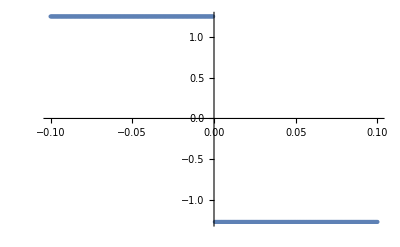

```mathematica
ListPlot[lll[[4]]]
```